## System Description

The system consists of two individual thermal transistors T_1 and T_2, connected in a Darlington pair configuration. The thermal flow between T_1 and T_2 is mediated via an intermediate energy divider mechanism. 
T_1 - Connected to two thermal baths, B_HOT (collector), B_CNT (base) and emitter connected to the HIGH side of the energy divider
T_2 - Connected to two thermal baths, B_HOT (collector), B_COL (emitter) and base connected to the LOW side of the energy divider

The thermal bath B_HOT is at a high temperature, while B_COL is at a low temperature. The temperature T_CNT of control terminal  B_CNT can be varied.
The energy divider mechanism receives and transmits energy to the two transistors.

Each transistor is modelled individually using the techniques developed for Optically Controlled Quantum Thermal Gate paper. However, we use a simplified 4×4 density matrix model instead of the previous 8×8 model. This is only valid under the conditions
	1. ω_L^S=ω_M^S=ω_R^S = 0
	2. ω_RL^S=0

The main reason for this is simplicity. Under a N-level energy divider and 8-level transistor model, we would have a 8×8×N = 64N dimensional vector space. This reduces to a 4×4×N = 16N level space under a 4-level transistor model.

The previous transistor eigenstates group together in groups of 2,
|1> = |+z,+z,+z> = |-z,-z,-z>
|2> = |+z,+z,-z> = |-z,-z,+z>
|3> =|+z,-z,+z> = |-z,+z,-z> 
|4> =|+z,-z,-z> = |-z,+z,+z>

## Energy divider parameters

N is the total number of quantum states in the intermediate energy divider.
p is the number of jumps in the HIGH side.
q is the number of jumps in the LOW side.
This makes a q/p energy divider.

```mathematica
Ns=4;p=3;q=1;
```

The intermediate energy divider regulates the energy flow between the |3_T_1>↔|4_T_1> transition of the first transistor, and the |2_T_2><->|4_T_2> transition of the second transistor.
However, the|2_T_1>↔|1_T_1> transition of the first transistor, needs also be considered since they have the same transition frequency as the |3_T_1>↔|4_T_1> transition.

To properly match the energy levels in the HIGH and LOW sides, we need the conditions,
	1. ω_MR^T_1≃p ω_ED
	2. ω_MR^T_2-ω_LM^T_2 ≃q ω_ED
where ℏ ω_ED is the energy of the intermediate harmonic oscillator.

## Some color definitions

```mathematica
BlueC=RGBColor[0.2627,0.4313,1];
PurpleC=RGBColor[0.5411,0.0784,0.9607];
RedC=RGBColor[0.60,0.30,0];
```

## System Hamiltonians

Identity operator

```mathematica
Id[ve_,ho_]:=ve,ho
```

### Subsystem Hamiltonians

The system contains three subsystems T_1, T_2 and T_ED. 
T_1 and T_2 are thermal transistors modelled as 4-level systems. T_ED is a harmonic oscillator truncated at N levels.

#### Transistor Hamiltonian

Transistor Hamiltonian consists of two parts,
	1) The first part consists of the ultrastrong coupling between the three TLSs

```mathematica
HsT1Sep[veT1_,hoT1_,veED_,hoED_,veT2_,hoT2_]:=({{1/2 ℏ (Subscript[ωLM, 1]+Subscript[ωMR, 1]), 0, 0, 0}, {0, 1/2 ℏ (Subscript[ωLM, 1]-Subscript[ωMR, 1]), 0, 0}, {0, 0, -1/2 ℏ (Subscript[ωLM, 1]+Subscript[ωMR, 1]), 0}, {0, 0, 0, 1/2 ℏ (-Subscript[ωLM, 1]+Subscript[ωMR, 1])}})[[veT1,hoT1]]Id[veED,hoED]Id[veT2,hoT2]
HsT2Sep[veT1_,hoT1_,veED_,hoED_,veT2_,hoT2_]:=Id[veT1,hoT1]Id[veED,hoED]({{1/2 ℏ (Subscript[ωLM, 2]+Subscript[ωMR, 2]), 0, 0, 0}, {0, 1/2 ℏ (Subscript[ωLM, 2]-Subscript[ωMR, 2]), 0, 0}, {0, 0, -1/2 ℏ (Subscript[ωLM, 2]+Subscript[ωMR, 2]), 0}, {0, 0, 0, 1/2 ℏ (-Subscript[ωLM, 2]+Subscript[ωMR, 2])}})[[veT2,hoT2]]
```

2) The second part consists of the field interactions with the external, tuned, electromagnetic field. The Hamiltonian below is given in its Schrodinger picture representation.

```mathematica
HlT1Sep[veT1_,hoT1_,veED_,hoED_,veT2_,hoT2_]:=({{0, 0, 0, 0}, {0, 0, 0, -(ℏ Subscript[Ω, 1])/2 ⅇ^(-ⅈ t (Subscript[ωLM, 1]-Subscript[ωMR, 1]))}, {0, 0, 0, 0}, {0, -(ℏ Subscript[Ω, 1])/2 ⅇ^(+ⅈ t (Subscript[ωLM, 1]-Subscript[ωMR, 1])), 0, 0}})[[veT1,hoT1]]Id[veED,hoED]Id[veT2,hoT2]
HlT2Sep[veT1_,hoT1_,veED_,hoED_,veT2_,hoT2_]:=Id[veT1,hoT1]Id[veED,hoED]({{0, 0, 0, 0}, {0, 0, 0, -(ℏ Subscript[Ω, 2])/2 ⅇ^(-ⅈ t (Subscript[ωLM, 2]-Subscript[ωMR, 2]))}, {0, 0, 0, 0}, {0, -(ℏ Subscript[Ω, 2])/2 ⅇ^(+ⅈ t (Subscript[ωLM, 2]-Subscript[ωMR, 2])), 0, 0}})[[veT2,hoT2]]
```

#### Energy divider Hamiltonian

```mathematica
Table[ℏ ωED(Ns-veED)veED,hoED,{veED,1,Ns},{hoED,1,Ns}]//MatrixForm
```

(3 ωED ℏ | 0 | 0 | 0
0 | 2 ωED ℏ | 0 | 0
0 | 0 | ωED ℏ | 0
0 | 0 | 0 | 0)

```mathematica
HsEDSep[veT1_,hoT1_,veED_,hoED_,veT2_,hoT2_]:=Id[veT1,hoT1](ℏ ωED(Ns-veED)veED,hoED)Id[veT2,hoT2]
```

### Forming the combined system Hamiltonian

The total number of combined system eigenstates are 4×N×4 = 16N.

In the matrix representation, we enumerate the energy levels as |(state of T_1) , (state of T_ED),(state of T_2)>
The energy levels are enumerated the following way

|1>	= |1,N-1,1>
|2>	= |1,N-1,2>
|3>	= |1,N-1,3>
|4>	= |1,N-1,4>
|5> 	= |1,N-2,1>
|6> 	= |1,N-2,2>
....
|16N-3>	= |4,0,1>
|16N-2>	= |4,0,2>
|16N-1>	= |4,0,3>
|16N> 	= |4,0,4>

Eigenstate mapping function, maps overall state (1 to 16N) to subsystem T_1, T_ED, T_2 state,

```mathematica
EmapT1[i_]:=Quotient[i-1,4Ns]+1
EmapED[i_]:=Quotient[QuotientRemainder[i-1,4Ns][[2]],4]+1
EmapT2[i_]:=QuotientRemainder[i-1,4][[2]]+1
```

```mathematica
Table[EmapT1[i],{i,1,16Ns}]
Table[EmapED[i],{i,1,16Ns}]
Table[EmapT2[i],{i,1,16Ns}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}

{1,1,1,1,2,2,2,2,3,3,3,3,4,4,4,4,1,1,1,1,2,2,2,2,3,3,3,3,4,4,4,4,1,1,1,1,2,2,2,2,3,3,3,3,4,4,4,4,1,1,1,1,2,2,2,2,3,3,3,3,4,4,4,4}

{1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4}

Matrix form of the three Hamiltonians

```mathematica
HsT1[ve_,ho_]:=HsT1Sep[EmapT1[ve],EmapT1[ho],EmapED[ve],EmapED[ho],EmapT2[ve],EmapT2[ho]]
HsED[ve_,ho_]:=HsEDSep[EmapT1[ve],EmapT1[ho],EmapED[ve],EmapED[ho],EmapT2[ve],EmapT2[ho]]
HsT2[ve_,ho_]:=HsT2Sep[EmapT1[ve],EmapT1[ho],EmapED[ve],EmapED[ho],EmapT2[ve],EmapT2[ho]]

HlT1[ve_,ho_]:=HlT1Sep[EmapT1[ve],EmapT1[ho],EmapED[ve],EmapED[ho],EmapT2[ve],EmapT2[ho]]
HlT2[ve_,ho_]:=HlT2Sep[EmapT1[ve],EmapT1[ho],EmapED[ve],EmapED[ho],EmapT2[ve],EmapT2[ho]]
```

Non-interacting subsystem Hamiltonians as a matrix in the combined system space (We consider the field interaction (Ĥ)_(field-sys)^S as a perturbation. Hence it is not included here, but in the Hsys1Matrix).

```mathematica
Hsys0Matrix = Table[HsT1[ve,ho]+HsED[ve,ho]+HsT2[ve,ho],{ve,1,16Ns},{ho,1,16Ns}];

Hsys0EVal[i_]:=Diagonal[Hsys0Matrix][[i]]
Diagonal[Hsys0Matrix]//MatrixForm
```

(3 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
3 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
3 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
3 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
3 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
3 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
3 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
3 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
1/2 ℏ (ωLM_1-ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
3 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
3 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
3 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
3 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
-1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
3 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
3 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
3 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
3 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
1/2 ℏ (-ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2))

## Interaction Hamiltonian between the subsystems

The interactions between the subsystems are considered WEAK enough such that the local master equation approach is justified.
This effectively means that the subsystem interactions should not significantly change the energy levels dictated by the non-interacting Hamiltonian.

The energy levels of the individual components are specially tuned in our model. 
	1. First of all, there are no direct interactions between T_1 and T_2.
	2. The energy levels are prepared so that
		ω_MR^T_1≃p ω_ED
		ω_MR^T_2-ω_LM^T_2 ≃q ω_ED
	3. Therefore the interactions are such that
		a) T_1 jumps up from |3_T_1> to |4_T_1> (or |2_T_1> to |1_T_1> ) while the HO jumps down p steps from |(m+p)_T_ED> to |m_T_ED> (and vice versa).
		b) T_2 jumps up from |2_T_2> to |4_T_2> while the HO jumps down q steps from |(m+q)_T_ED> to |m_T_ED> (and vice versa).
	3. The interaction strengths between subsystems are given by γ_T_1[m] and γ_T_2[m] with m enumerating the different start (or end) state of the HO.

First define some necessary matrices

```mathematica
OneMatrix[ve_,ho_,n_]:=Table[ve,i ho,j,{i,1,n},{j,1,n}]
{{OneMatrix[Ns-m,Ns-(m+p),Ns]/.m->0//MatrixForm,OneMatrix[Ns-(m+p),Ns-m,Ns]/.m->0//MatrixForm},
{OneMatrix[Ns-m,Ns-(m+q),Ns]/.m->0//MatrixForm,OneMatrix[Ns-(m+q),Ns-m,Ns]/.m->0//MatrixForm},
{OneMatrix[Ns-m,Ns-(m+q),Ns]/.m->1//MatrixForm,OneMatrix[Ns-(m+q),Ns-m,Ns]/.m->1//MatrixForm},
{OneMatrix[Ns-m,Ns-(m+q),Ns]/.m->2//MatrixForm,OneMatrix[Ns-(m+q),Ns-m,Ns]/.m->2//MatrixForm}}
```

{{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}}

Considering the above Hamiltonian, we write the interaction between T_1 and T_ED as,

```mathematica
HintT1andED[ve_,ho_]:=(∑_(m=0)^(Ns-1-p) (ℏ γT1[m]KroneckerProduct[(KroneckerProduct[({{0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}}),OneMatrix[Ns-m,Ns-(m+p),Ns]]+KroneckerProduct[({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}}),OneMatrix[Ns-(m+p),Ns-m,Ns]]),IdentityMatrix[4]]))[[ve,ho]]
```

Similarly, we write the interaction between T_ED and T_2 as,

```mathematica
HintEDandT2[ve_,ho_]:=(∑_(m=0)^(Ns-1-q) (ℏ γT2[m]KroneckerProduct[IdentityMatrix[4],(KroneckerProduct[OneMatrix[Ns-m,Ns-(m+q),Ns],({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 1, 0, 0}})]+KroneckerProduct[OneMatrix[Ns-(m+q),Ns-m,Ns],({{0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}})])]))[[ve,ho]]
```

Interacting system Hamiltonian as a matrix in the combined system space

```mathematica
Hsys1Matrix = Table[HintT1andED[ve,ho]+HintEDandT2[ve,ho],{ve,1,16Ns},{ho,1,16Ns}];
Hsys2Matrix = Table[HlT1[ve,ho],{ve,1,16Ns},{ho,1,16Ns}];
Hsys3Matrix = Table[HlT2[ve,ho],{ve,1,16Ns},{ho,1,16Ns}];
{MatrixForm[Hsys1Matrix],MatrixForm[Hsys2Matrix],MatrixForm[Hsys3Matrix]}
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ℏ γT2[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0)}

## Combined system Hamiltonian

```mathematica
HsysMatrix=Hsys0Matrix+Hsys1Matrix+Hsys2Matrix+Hsys3Matrix;
MatrixForm[HsysMatrix]
```

(3 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 3 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ℏ γT2[2] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 3 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 3 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 3 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 3 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[2] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_1-ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 3 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[2] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | -1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 3 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[2] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (-ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2))

## Density Matrix

In the combined system, the density matrix is 4N×4N=16N.

```mathematica
ρMatrix[t_]:=Table[Subscript[ρ, ve,ho][t],{ve,1,16Ns},{ho,1,16Ns}]
```

```mathematica
MatrixForm[ρMatrix[t]]
```

(1)
 |  |  |  |

## System-bath interactions

The inter-subsystem interaction Hamiltonian is supposed to be in the weak regime. The energy eigensystems of the individual subsystems are minimally affected by this interaction.
This means that it is enough to model the thermal interactions in the bare eigensystem of only the individual transistor Hamiltonians.

### Thermal interactions of individual transistors

In the simplified individual transistor model, each bath has two Lindblad operators

```mathematica
Subscript[LinOps, S_,P_][i_]:=({{({{0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}), ({{0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})}, {({{0, 0, 1, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}), ({{0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}})}, {({{0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}), ({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}})}})[[P,i]]
Subscript[ωLinOps, S_,P_][i_]:=({{-Subscript[ωLM, S], -Subscript[ωLM, S]}, {-Subscript[ωLM, S]-Subscript[ωMR, S], -Subscript[ωLM, S]+Subscript[ωMR, S]}, {-Subscript[ωMR, S], Subscript[ωMR, S]}})[[P,i]]
```

### Interactions of the hot bath B_HOT

B_HOT is connected to the collectors of both T_1 and T_2. Hence, we need to extract the S=1, P=1 and S=2, P=1 Lindblad operators. To convert to the full 16N space, we need to expand the operators using proper identity matrices.

```mathematica
AMatrixT1BHOT[i_]:=KroneckerProduct[Subscript[LinOps, 1,1][i],KroneckerProduct[IdentityMatrix[Ns],IdentityMatrix[4]]]
ωT1BHOT[i_]:=Subscript[ωLinOps, 1,1][i]
AMatrixT2BHOT[i_]:=KroneckerProduct[IdentityMatrix[4],KroneckerProduct[IdentityMatrix[Ns],Subscript[LinOps, 2,1][i]]]
ωT2BHOT[i_]:=Subscript[ωLinOps, 2,1][i]
```

```mathematica
Table[MatrixForm[AMatrixT1BHOT[i]],{i,1,2}];
Table[MatrixForm[AMatrixT2BHOT[i]],{i,1,2}];
Table[MatrixForm[ωT1BHOT[i]],{i,1,2}]
Table[MatrixForm[ωT2BHOT[i]],{i,1,2}]
```

{-ωLM_1,-ωLM_1}

{-ωLM_2,-ωLM_2}

### Interactions of the control bath B_CNT

B_CNT is connected to the base of T_1. Hence, we need to extract the S=1, P=2 Lindblad operators. To convert to the full 16N space, we need to expand the operators using proper identity matrices.

```mathematica
AMatrixT1BCNT[i_]:=KroneckerProduct[Subscript[LinOps, 1,2][i],KroneckerProduct[IdentityMatrix[Ns],IdentityMatrix[4]]]
ωT1BCNT[i_]:=Subscript[ωLinOps, 1,2][i]
```

```mathematica
Table[MatrixForm[AMatrixT1BCNT[i]],{i,1,2}];
Table[MatrixForm[ωT1BCNT[i]],{i,1,2}]
```

{-ωLM_1-ωMR_1,-ωLM_1+ωMR_1}

### Interactions of the cold bath B_COL

B_COL is connected to the emitter of T_2. Hence, we need to extract the S=2, P=3 Lindblad operators. To convert to the full 16N space, we need to expand the operators using proper identity matrices.

```mathematica
AMatrixT2BCOL[i_]:=KroneckerProduct[IdentityMatrix[4],KroneckerProduct[IdentityMatrix[Ns],Subscript[LinOps, 2,3][i]]]
ωT2BCOL[i_]:=Subscript[ωLinOps, 2,3][i]
```

```mathematica
Table[MatrixForm[AMatrixT2BCOL[i]],{i,1,2}];
Table[MatrixForm[ωT2BCOL[i]],{i,1,2}]
```

{-ωMR_2,ωMR_2}

### Lindblad terms of the master equation

```mathematica
LinTerm[ρ_,A_,J_,NBE_,ω_]:=∑_(i=1)^2 (J[ω[i]](1+NBE[ω[i]])(A[i].ρ.A[i]†-1/2(A[i]†.A[i].ρ+ρ.A[i]†.A[i]))+J[ω[i]]NBE[ω[i]](A[i]†.ρ.A[i]-1/2(A[i].A[i]†.ρ+ρ.A[i].A[i]†)))
```

```mathematica
LinMatrixT1BHOT[ρ_]:=LinMatrixT1BHOT[ρ]=LinTerm[ρ,AMatrixT1BHOT,Subscript[J, 1],Subscript[NBE, 1],ωT1BHOT]
LinMatrixT2BHOT[ρ_]:=LinMatrixT2BHOT[ρ]=LinTerm[ρ,AMatrixT2BHOT,Subscript[J, 1],Subscript[NBE, 1],ωT2BHOT]
LinMatrixT1BCNT[ρ_]:=LinMatrixT1BCNT[ρ]=LinTerm[ρ,AMatrixT1BCNT,Subscript[J, 2],Subscript[NBE, 2],ωT1BCNT]
LinMatrixT2BCOL[ρ_]:=LinMatrixT2BCOL[ρ]=LinTerm[ρ,AMatrixT2BCOL,Subscript[J, 3],Subscript[NBE, 3],ωT2BCOL]
```

```mathematica
MatrixForm[Simplify[LinMatrixT1BHOT[ρMatrix[t]]]]
MatrixForm[Simplify[LinMatrixT2BHOT[ρMatrix[t]]]]
MatrixForm[Simplify[LinMatrixT1BCNT[ρMatrix[t]]]]
MatrixForm[Simplify[LinMatrixT2BCOL[ρMatrix[t]]]]
```

(1)
 |  |  |  |

(1)
 |  |  |  |

(1)
 |  |  |  |

«1 more identical outputs»

## Defining the interaction picture

```mathematica
Hsys1INTMatrix = Simplify[MatrixExp[+(ⅈ t)/ℏ Hsys0Matrix].Hsys1Matrix.MatrixExp[-(ⅈ t)/ℏ Hsys0Matrix]];
Hsys2INTMatrix = Simplify[MatrixExp[+(ⅈ t)/ℏ Hsys0Matrix].Hsys2Matrix.MatrixExp[-(ⅈ t)/ℏ Hsys0Matrix]];
Hsys3INTMatrix = Simplify[MatrixExp[+(ⅈ t)/ℏ Hsys0Matrix].Hsys3Matrix.MatrixExp[-(ⅈ t)/ℏ Hsys0Matrix]];
MatrixForm[Hsys1INTMatrix+Hsys2INTMatrix+Hsys3INTMatrix]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[2] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (3 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | ⅇ^(-ⅈ t (3 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (3 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (3 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (3 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (3 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (3 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (3 ωED-ωMR_1)) ℏ γT1[0] | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[2] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (3 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (3 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (3 ωED-ωMR_1)) ℏ γT1[0] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (3 ωED-ωMR_1)) ℏ γT1[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[2] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[2] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | ⅇ^(-ⅈ t (3 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | ⅇ^(-ⅈ t (3 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | ⅇ^(-ⅈ t (3 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | ⅇ^(-ⅈ t (3 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0)

Simplify the Hamiltonian for the fully resonant case,

```mathematica
Hsys1INTMatrix = Simplify[MatrixExp[+(ⅈ t)/ℏ Hsys0Matrix].Hsys1Matrix.MatrixExp[-(ⅈ t)/ℏ Hsys0Matrix]//.{ωED->Subscript[ωMR, 1]/p,Subscript[ωMR, 1]->p/q(Subscript[ωMR, 2]-Subscript[ωLM, 2])}];
Hsys2INTMatrix = Simplify[MatrixExp[+(ⅈ t)/ℏ Hsys0Matrix].Hsys2Matrix.MatrixExp[-(ⅈ t)/ℏ Hsys0Matrix]//.{ωED->Subscript[ωMR, 1]/p,Subscript[ωMR, 1]->p/q(Subscript[ωMR, 2]-Subscript[ωLM, 2])}];
Hsys3INTMatrix = Simplify[MatrixExp[+(ⅈ t)/ℏ Hsys0Matrix].Hsys3Matrix.MatrixExp[-(ⅈ t)/ℏ Hsys0Matrix]//.{ωED->Subscript[ωMR, 1]/p,Subscript[ωMR, 1]->p/q(Subscript[ωMR, 2]-Subscript[ωLM, 2])}];
MatrixForm[Hsys1INTMatrix+Hsys2INTMatrix+Hsys3INTMatrix]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ℏ γT2[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ℏ γT2[2] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ℏ γT2[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[2] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ℏ γT2[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[2] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ℏ γT2[2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[2] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ℏ γT2[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0)

## Quantum Markovian master equation

Ohmic bath spectral density,

```mathematica
Jassum=Subscript[J, P_][ω_]->Subscript[κ, P] ω;
```

Right hand side of the Markovian quantum master equation (in interaction picture),

```mathematica
RHSengdiv=-ⅈ/ℏ(Hsys1INTMatrix.ρMatrix[t]-ρMatrix[t].Hsys1INTMatrix);
Subscript[RHSfield, 1]=-ⅈ/ℏ(Hsys2INTMatrix.ρMatrix[t]-ρMatrix[t].Hsys2INTMatrix);
Subscript[RHSfield, 2]=-ⅈ/ℏ(Hsys3INTMatrix.ρMatrix[t]-ρMatrix[t].Hsys3INTMatrix);
```

```mathematica
RHS=RHSengdiv+Subscript[RHSfield, 1]+Subscript[RHSfield, 2]+LinMatrixT1BHOT[ρMatrix[t]]+LinMatrixT2BHOT[ρMatrix[t]]+LinMatrixT1BCNT[ρMatrix[t]]+LinMatrixT2BCOL[ρMatrix[t]];
RHS=Collect[RHS,Flatten[{Table[{Subscript[J, P][ω_]},{P,1,3}],Subscript[Ω, 1],Subscript[Ω, 2],Table[γT1[i],{i,0,Ns-1-p}],Table[γT2[i],{i,0,Ns-1-q}]}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,16Ns},{j,1,16Ns}]]]&];
```

Left hand side of the Markovian quantum master equation (in interaction picture),

```mathematica
LHS=D[ρMatrix[t], t];
MatrixForm[%]
```

(1)
 |  |  |  |

Markovian quantum master equation for a general density matrix,

```mathematica
sol=Flatten[Solve[LHS==RHS,Flatten[Table[Subscript[ρ, i,j]'[t],{i,1,16Ns},{j,1,16Ns}]]]/.Rule->Equal];
```

```mathematica
sol=ApplySides[Collect[Expand[#],Flatten[{Table[{Subscript[J, P][ω_]},{P,1,3}],Subscript[Ω, 1],Subscript[Ω, 2],Table[γT1[i],{i,0,Ns-1-p}],Table[γT2[i],{i,0,Ns-1-q}]}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,16Ns},{j,1,16Ns}]]]&]&,sol];
```

Separate diagonal and off diagonal equations,

```mathematica
soldiag=sol[[1;; ;;(16Ns+1)]];
soloffdiag=Delete[sol,Table[{1+(16Ns+1)i},{i,0,(16Ns-1)}]];
```

Net thermal decaying rate Τ_(S,P)[i,j] of component S from state | i > to state | j > while releasing energy to reservoir P. Note i > j.
Τs_(S,P)[i,j] is used due to variable naming issues.

```mathematica
Subscript[ω, i_,j_]:=Simplify[1/ℏ(Hsys0EVal[i]-Hsys0EVal[j])]
Subscript[Τs, P_][i_,j_]:=Subscript[J, P][Subscript[ω, i,j]]((1+Subscript[NBE, P][Subscript[ω, i,j]])Subscript[ρ, i,i][t]-Subscript[NBE, P][Subscript[ω, i,j]]Subscript[ρ, j,j][t])
Subscript[Τsm, P_][i_,j_]:=Subscript[J, P][Subscript[ω, i,j]](Subscript[NBE, P][Subscript[ω, i,j]]Subscript[ρ, j,j][t]+(-1-Subscript[NBE, P][Subscript[ω, i,j]])Subscript[ρ, i,i][t])
```

Net optical field induced decaying rate Υ_P[i,j] of the device P from state | i > to state | j > while absorbing energy from the external electric field.
Υs[i,j] is used due to variable naming issues.

```mathematica
Subscript[Υs, S_][i_,j_]:= Subscript[Ω, S](1/2 ⅈ Subscript[ρ, i,j][t]-1/2 ⅈ Subscript[ρ, j,i][t])
```

Diagonal equations in simplified form

```mathematica
soldiag/.Flatten[{Table[Subscript[Τs, P][i,j]->Subscript[Τ, P][i,j] ,{P,1,3},{i,1,16Ns},{j,1,16Ns}],Table[Subscript[Τsm, P][i,j]->-Subscript[Τ, P][i,j] ,{P,1,3},{i,1,16Ns},{j,1,16Ns}],Table[Subscript[Υs, S][i,j]->Subscript[Υ, S][i,j] ,{S,1,2},{i,1,16Ns},{j,1,i-1}],Table[Subscript[Υs, S][i,j]->Subscript[Υ, S][i,j] ,{S,1,2},{j,1,16Ns},{i,1,j-1}]}];
%//MatrixForm
```

(ρ_(1,1)'[t]==Τ_1[4,1]+Τ_1[49,1]+Τ_2[33,1]+Τ_3[2,1]
ρ_(2,2)'[t]==Τ_1[3,2]+Τ_1[50,2]+Τ_2[34,2]-Τ_3[2,1]+Υ_2[4,2]+γT2[2] (ⅈ ρ_(2,8)[t]-ⅈ ρ_(8,2)[t])
ρ_(3,3)'[t]==-Τ_1[3,2]+Τ_1[51,3]+Τ_2[35,3]+Τ_3[4,3]
ρ_(4,4)'[t]==-Τ_1[4,1]+Τ_1[52,4]+Τ_2[36,4]-Τ_3[4,3]+Υ_2[2,4]
ρ_(5,5)'[t]==Τ_1[8,5]+Τ_1[53,5]+Τ_2[37,5]+Τ_3[6,5]
ρ_(6,6)'[t]==Τ_1[7,6]+Τ_1[54,6]+Τ_2[38,6]-Τ_3[6,5]+Υ_2[8,6]+γT2[1] (ⅈ ρ_(6,12)[t]-ⅈ ρ_(12,6)[t])
ρ_(7,7)'[t]==-Τ_1[7,6]+Τ_1[55,7]+Τ_2[39,7]+Τ_3[8,7]
ρ_(8,8)'[t]==-Τ_1[8,5]+Τ_1[56,8]+Τ_2[40,8]-Τ_3[8,7]+Υ_2[6,8]+γT2[2] (-ⅈ ρ_(2,8)[t]+ⅈ ρ_(8,2)[t])
ρ_(9,9)'[t]==Τ_1[12,9]+Τ_1[57,9]+Τ_2[41,9]+Τ_3[10,9]
ρ_(10,10)'[t]==Τ_1[11,10]+Τ_1[58,10]+Τ_2[42,10]-Τ_3[10,9]+Υ_2[12,10]+γT2[0] (ⅈ ρ_(10,16)[t]-ⅈ ρ_(16,10)[t])
ρ_(11,11)'[t]==-Τ_1[11,10]+Τ_1[59,11]+Τ_2[43,11]+Τ_3[12,11]
ρ_(12,12)'[t]==-Τ_1[12,9]+Τ_1[60,12]+Τ_2[44,12]-Τ_3[12,11]+Υ_2[10,12]+γT2[1] (-ⅈ ρ_(6,12)[t]+ⅈ ρ_(12,6)[t])
ρ_(13,13)'[t]==Τ_1[16,13]+Τ_1[61,13]+Τ_2[45,13]+Τ_3[14,13]+γT1[0] (ⅈ ρ_(13,17)[t]-ⅈ ρ_(17,13)[t])
ρ_(14,14)'[t]==Τ_1[15,14]+Τ_1[62,14]+Τ_2[46,14]-Τ_3[14,13]+Υ_2[16,14]+γT1[0] (ⅈ ρ_(14,18)[t]-ⅈ ρ_(18,14)[t])
ρ_(15,15)'[t]==-Τ_1[15,14]+Τ_1[63,15]+Τ_2[47,15]+Τ_3[16,15]+γT1[0] (ⅈ ρ_(15,19)[t]-ⅈ ρ_(19,15)[t])
ρ_(16,16)'[t]==-Τ_1[16,13]+Τ_1[64,16]+Τ_2[48,16]-Τ_3[16,15]+Υ_2[14,16]+γT2[0] (-ⅈ ρ_(10,16)[t]+ⅈ ρ_(16,10)[t])+γT1[0] (ⅈ ρ_(16,20)[t]-ⅈ ρ_(20,16)[t])
ρ_(17,17)'[t]==Τ_1[20,17]+Τ_1[33,17]+Τ_2[49,17]+Τ_3[18,17]+Υ_1[49,17]+γT1[0] (-ⅈ ρ_(13,17)[t]+ⅈ ρ_(17,13)[t])
ρ_(18,18)'[t]==Τ_1[19,18]+Τ_1[34,18]+Τ_2[50,18]-Τ_3[18,17]+Υ_1[50,18]+Υ_2[20,18]+γT1[0] (-ⅈ ρ_(14,18)[t]+ⅈ ρ_(18,14)[t])+γT2[2] (ⅈ ρ_(18,24)[t]-ⅈ ρ_(24,18)[t])
ρ_(19,19)'[t]==-Τ_1[19,18]+Τ_1[35,19]+Τ_2[51,19]+Τ_3[20,19]+Υ_1[51,19]+γT1[0] (-ⅈ ρ_(15,19)[t]+ⅈ ρ_(19,15)[t])
ρ_(20,20)'[t]==-Τ_1[20,17]+Τ_1[36,20]+Τ_2[52,20]-Τ_3[20,19]+Υ_1[52,20]+Υ_2[18,20]+γT1[0] (-ⅈ ρ_(16,20)[t]+ⅈ ρ_(20,16)[t])
ρ_(21,21)'[t]==Τ_1[24,21]+Τ_1[37,21]+Τ_2[53,21]+Τ_3[22,21]+Υ_1[53,21]
ρ_(22,22)'[t]==Τ_1[23,22]+Τ_1[38,22]+Τ_2[54,22]-Τ_3[22,21]+Υ_1[54,22]+Υ_2[24,22]+γT2[1] (ⅈ ρ_(22,28)[t]-ⅈ ρ_(28,22)[t])
ρ_(23,23)'[t]==-Τ_1[23,22]+Τ_1[39,23]+Τ_2[55,23]+Τ_3[24,23]+Υ_1[55,23]
ρ_(24,24)'[t]==-Τ_1[24,21]+Τ_1[40,24]+Τ_2[56,24]-Τ_3[24,23]+Υ_1[56,24]+Υ_2[22,24]+γT2[2] (-ⅈ ρ_(18,24)[t]+ⅈ ρ_(24,18)[t])
ρ_(25,25)'[t]==Τ_1[28,25]+Τ_1[41,25]+Τ_2[57,25]+Τ_3[26,25]+Υ_1[57,25]
ρ_(26,26)'[t]==Τ_1[27,26]+Τ_1[42,26]+Τ_2[58,26]-Τ_3[26,25]+Υ_1[58,26]+Υ_2[28,26]+γT2[0] (ⅈ ρ_(26,32)[t]-ⅈ ρ_(32,26)[t])
ρ_(27,27)'[t]==-Τ_1[27,26]+Τ_1[43,27]+Τ_2[59,27]+Τ_3[28,27]+Υ_1[59,27]
ρ_(28,28)'[t]==-Τ_1[28,25]+Τ_1[44,28]+Τ_2[60,28]-Τ_3[28,27]+Υ_1[60,28]+Υ_2[26,28]+γT2[1] (-ⅈ ρ_(22,28)[t]+ⅈ ρ_(28,22)[t])
ρ_(29,29)'[t]==Τ_1[32,29]+Τ_1[45,29]+Τ_2[61,29]+Τ_3[30,29]+Υ_1[61,29]
ρ_(30,30)'[t]==Τ_1[31,30]+Τ_1[46,30]+Τ_2[62,30]-Τ_3[30,29]+Υ_1[62,30]+Υ_2[32,30]
ρ_(31,31)'[t]==-Τ_1[31,30]+Τ_1[47,31]+Τ_2[63,31]+Τ_3[32,31]+Υ_1[63,31]
ρ_(32,32)'[t]==-Τ_1[32,29]+Τ_1[48,32]+Τ_2[64,32]-Τ_3[32,31]+Υ_1[64,32]+Υ_2[30,32]+γT2[0] (-ⅈ ρ_(26,32)[t]+ⅈ ρ_(32,26)[t])
ρ_(33,33)'[t]==-Τ_1[33,17]+Τ_1[36,33]-Τ_2[33,1]+Τ_3[34,33]+γT1[0] (ⅈ ρ_(33,61)[t]-ⅈ ρ_(61,33)[t])
ρ_(34,34)'[t]==-Τ_1[34,18]+Τ_1[35,34]-Τ_2[34,2]-Τ_3[34,33]+Υ_2[36,34]+γT2[2] (ⅈ ρ_(34,40)[t]-ⅈ ρ_(40,34)[t])+γT1[0] (ⅈ ρ_(34,62)[t]-ⅈ ρ_(62,34)[t])
ρ_(35,35)'[t]==-Τ_1[35,19]-Τ_1[35,34]-Τ_2[35,3]+Τ_3[36,35]+γT1[0] (ⅈ ρ_(35,63)[t]-ⅈ ρ_(63,35)[t])
ρ_(36,36)'[t]==-Τ_1[36,20]-Τ_1[36,33]-Τ_2[36,4]-Τ_3[36,35]+Υ_2[34,36]+γT1[0] (ⅈ ρ_(36,64)[t]-ⅈ ρ_(64,36)[t])
ρ_(37,37)'[t]==-Τ_1[37,21]+Τ_1[40,37]-Τ_2[37,5]+Τ_3[38,37]
ρ_(38,38)'[t]==-Τ_1[38,22]+Τ_1[39,38]-Τ_2[38,6]-Τ_3[38,37]+Υ_2[40,38]+γT2[1] (ⅈ ρ_(38,44)[t]-ⅈ ρ_(44,38)[t])
ρ_(39,39)'[t]==-Τ_1[39,23]-Τ_1[39,38]-Τ_2[39,7]+Τ_3[40,39]
ρ_(40,40)'[t]==-Τ_1[40,24]-Τ_1[40,37]-Τ_2[40,8]-Τ_3[40,39]+Υ_2[38,40]+γT2[2] (-ⅈ ρ_(34,40)[t]+ⅈ ρ_(40,34)[t])
ρ_(41,41)'[t]==-Τ_1[41,25]+Τ_1[44,41]-Τ_2[41,9]+Τ_3[42,41]
ρ_(42,42)'[t]==-Τ_1[42,26]+Τ_1[43,42]-Τ_2[42,10]-Τ_3[42,41]+Υ_2[44,42]+γT2[0] (ⅈ ρ_(42,48)[t]-ⅈ ρ_(48,42)[t])
ρ_(43,43)'[t]==-Τ_1[43,27]-Τ_1[43,42]-Τ_2[43,11]+Τ_3[44,43]
ρ_(44,44)'[t]==-Τ_1[44,28]-Τ_1[44,41]-Τ_2[44,12]-Τ_3[44,43]+Υ_2[42,44]+γT2[1] (-ⅈ ρ_(38,44)[t]+ⅈ ρ_(44,38)[t])
ρ_(45,45)'[t]==-Τ_1[45,29]+Τ_1[48,45]-Τ_2[45,13]+Τ_3[46,45]
ρ_(46,46)'[t]==-Τ_1[46,30]+Τ_1[47,46]-Τ_2[46,14]-Τ_3[46,45]+Υ_2[48,46]
ρ_(47,47)'[t]==-Τ_1[47,31]-Τ_1[47,46]-Τ_2[47,15]+Τ_3[48,47]
ρ_(48,48)'[t]==-Τ_1[48,32]-Τ_1[48,45]-Τ_2[48,16]-Τ_3[48,47]+Υ_2[46,48]+γT2[0] (-ⅈ ρ_(42,48)[t]+ⅈ ρ_(48,42)[t])
ρ_(49,49)'[t]==-Τ_1[49,1]+Τ_1[52,49]-Τ_2[49,17]+Τ_3[50,49]+Υ_1[17,49]
ρ_(50,50)'[t]==-Τ_1[50,2]+Τ_1[51,50]-Τ_2[50,18]-Τ_3[50,49]+Υ_1[18,50]+Υ_2[52,50]+γT2[2] (ⅈ ρ_(50,56)[t]-ⅈ ρ_(56,50)[t])
ρ_(51,51)'[t]==-Τ_1[51,3]-Τ_1[51,50]-Τ_2[51,19]+Τ_3[52,51]+Υ_1[19,51]
ρ_(52,52)'[t]==-Τ_1[52,4]-Τ_1[52,49]-Τ_2[52,20]-Τ_3[52,51]+Υ_1[20,52]+Υ_2[50,52]
ρ_(53,53)'[t]==-Τ_1[53,5]+Τ_1[56,53]-Τ_2[53,21]+Τ_3[54,53]+Υ_1[21,53]
ρ_(54,54)'[t]==-Τ_1[54,6]+Τ_1[55,54]-Τ_2[54,22]-Τ_3[54,53]+Υ_1[22,54]+Υ_2[56,54]+γT2[1] (ⅈ ρ_(54,60)[t]-ⅈ ρ_(60,54)[t])
ρ_(55,55)'[t]==-Τ_1[55,7]-Τ_1[55,54]-Τ_2[55,23]+Τ_3[56,55]+Υ_1[23,55]
ρ_(56,56)'[t]==-Τ_1[56,8]-Τ_1[56,53]-Τ_2[56,24]-Τ_3[56,55]+Υ_1[24,56]+Υ_2[54,56]+γT2[2] (-ⅈ ρ_(50,56)[t]+ⅈ ρ_(56,50)[t])
ρ_(57,57)'[t]==-Τ_1[57,9]+Τ_1[60,57]-Τ_2[57,25]+Τ_3[58,57]+Υ_1[25,57]
ρ_(58,58)'[t]==-Τ_1[58,10]+Τ_1[59,58]-Τ_2[58,26]-Τ_3[58,57]+Υ_1[26,58]+Υ_2[60,58]+γT2[0] (ⅈ ρ_(58,64)[t]-ⅈ ρ_(64,58)[t])
ρ_(59,59)'[t]==-Τ_1[59,11]-Τ_1[59,58]-Τ_2[59,27]+Τ_3[60,59]+Υ_1[27,59]
ρ_(60,60)'[t]==-Τ_1[60,12]-Τ_1[60,57]-Τ_2[60,28]-Τ_3[60,59]+Υ_1[28,60]+Υ_2[58,60]+γT2[1] (-ⅈ ρ_(54,60)[t]+ⅈ ρ_(60,54)[t])
ρ_(61,61)'[t]==-Τ_1[61,13]+Τ_1[64,61]-Τ_2[61,29]+Τ_3[62,61]+Υ_1[29,61]+γT1[0] (-ⅈ ρ_(33,61)[t]+ⅈ ρ_(61,33)[t])
ρ_(62,62)'[t]==-Τ_1[62,14]+Τ_1[63,62]-Τ_2[62,30]-Τ_3[62,61]+Υ_1[30,62]+Υ_2[64,62]+γT1[0] (-ⅈ ρ_(34,62)[t]+ⅈ ρ_(62,34)[t])
ρ_(63,63)'[t]==-Τ_1[63,15]-Τ_1[63,62]-Τ_2[63,31]+Τ_3[64,63]+Υ_1[31,63]+γT1[0] (-ⅈ ρ_(35,63)[t]+ⅈ ρ_(63,35)[t])
ρ_(64,64)'[t]==-Τ_1[64,16]-Τ_1[64,61]-Τ_2[64,32]-Τ_3[64,63]+Υ_1[32,64]+Υ_2[62,64]+γT1[0] (-ⅈ ρ_(36,64)[t]+ⅈ ρ_(64,36)[t])+γT2[0] (-ⅈ ρ_(58,64)[t]+ⅈ ρ_(64,58)[t]))

## Dynamical heat flows

Thermal distributions in the environments (Bose Einstein distribution),

```mathematica
NBEassum=Subscript[NBE, P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, P]))-1);
```

```mathematica
Manipulate[Plot[{Subscript[NBE, 1][ω]//.{NBEassum,k-> 1,ℏ->1,Subscript[T, 1]->T1},Subscript[NBE, 2][ω]//.{NBEassum,k-> 1,ℏ->1,Subscript[T, 2]->T2}},{ω,0,10 0.2},PlotRange-> {0,2},PlotLegends->{"L","R"},AxesLabel->{"ω","P[ω]"}]
,{{T1,0.2},0.01,1},{{T2,0.1},0.01,1}]
```

### Characterizing thermal flows

Use the first law of thermodynamics, the rate of change of internal energy of the system is equal to the energy inflows.
We can define four thermal flows into the system, two from B_H and one each from B_N and B_C. Similarly, two energy flows from the field to T_1 and T_2 can also be defined.

The system in this case is the two transistors and the energy divider. The field interactions are OUTSIDE the system.

∂_t <(Ĥ)_(T_1 T_2 ED)> = J_HOT^T_1[t]+J_HOT^T_2[t]+J_CNT^T_1[t]+J_COL^T_2[t]+J_F^T_1[t]+J_F^T_2[t]

(Ĥ)_(T_1 T_2 ED) = (Ĥ)_sys^0 + (Ĥ)_sys^1

From definition of expected values,

<(Ĥ)_(T_1 T_2 ED)> = Tr[(Ĥ)_(T_1 T_2 ED)ρ̂[t]] = Tr[(Ĥ)_(T_1 T_2 ED).MatrixExp[-ⅈ/ℏ(Ĥ)_sys^0 t].(ρ̂)_INT[t].MatrixExp[+ⅈ/ℏ(Ĥ)_sys^0 t]]
	= Tr[MatrixExp[+ⅈ/ℏ(Ĥ)_sys^0 t].(Ĥ)_(T_1 T_2 ED).MatrixExp[-ⅈ/ℏ(Ĥ)_sys^0 t].(ρ̂)_INT[t]]
	= Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t]).(ρ̂)_INT[t]]

where we used

(ρ̂)_INT[t] = MatrixExp[+ⅈ/ℏ(Ĥ)_sys^0 t].ρ̂[t].MatrixExp[-ⅈ/ℏ(Ĥ)_sys^0 t]
(Ĥ)_(sys,INT)^1[t] = MatrixExp[+ⅈ/ℏ(Ĥ)_sys^0 t].(Ĥ)_sys^1.MatrixExp[-ⅈ/ℏ(Ĥ)_sys^0 t]

Substituting the above expression,

∂_t <(Ĥ)_(T_1 T_2 ED)>  = ∂_t Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t]).(ρ̂)_INT[t]]
		= Tr[(∂_t ((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])).(ρ̂)_INT[t]]+Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t]).∂_t (ρ̂)_INT[t]]
		= Tr[(∂_t (Ĥ)_(sys,INT)^1[t]).(ρ̂)_INT[t]]+Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t]).(-ⅈ/ℏ[((Ĥ)_(sys,INT)^1[t]+(Ĥ)_(sys,INT)^2[t]+(Ĥ)_(sys,INT)^3[t]),(ρ̂)_INT[t]]+(ℒ̂)_HOT^T_1[(ρ̂)_INT[t]]+(ℒ̂)_HOT^T_2[(ρ̂)_INT[t]]+(ℒ̂)_CNT[(ρ̂)_INT[t]]+(ℒ̂)_COL[(ρ̂)_INT[t]])]
		= Tr[(∂_t (Ĥ)_(sys,INT)^1[t]).(ρ̂)_INT[t]]- ⅈ/ℏ Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t]).[((Ĥ)_(sys,INT)^1[t]+(Ĥ)_(sys,INT)^2[t]+(Ĥ)_(sys,INT)^3[t]),(ρ̂)_INT[t]]] +Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])(ℒ̂)_HOT^T_1[(ρ̂)_INT[t]]]+Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])(ℒ̂)_HOT^T_2[(ρ̂)_INT[t]]]+Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])(ℒ̂)_CNT[(ρ̂)_INT[t]]]+Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])(ℒ̂)_COL[(ρ̂)_INT[t]]]

For our particular interaction Hamiltonian, consider the first two terms alone

```mathematica
Tr[(D[Hsys1INTMatrix, t]).ρMatrix[t]]- ⅈ/ℏ Tr[(Hsys0Matrix+Hsys1INTMatrix).((Hsys1INTMatrix+Hsys2INTMatrix+Hsys3INTMatrix).ρMatrix[t]-ρMatrix[t].(Hsys1INTMatrix+Hsys2INTMatrix+Hsys3INTMatrix))]  //Simplify;
Tr[Subscript[RHSfield, 1].(Hsys0Matrix+Hsys1INTMatrix)]+Tr[Subscript[RHSfield, 2].(Hsys0Matrix+Hsys1INTMatrix)]//Simplify;
%%-%//.{ωED->Subscript[ωMR, 1]/p,Subscript[ωMR, 1]->p/q(Subscript[ωMR, 2]-Subscript[ωLM, 2])}//Simplify
```

0

Therefore we have

Tr[(∂_t (Ĥ)_(sys,INT)^1[t]).(ρ̂)_INT[t]]- ⅈ/ℏ Tr[((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t]).[((Ĥ)_(sys,INT)^1[t]+(Ĥ)_(sys,INT)^2[t]+(Ĥ)_(sys,INT)^3[t]),(ρ̂)_INT[t]]] = Tr[-ⅈ/ℏ[(Ĥ)_(sys,INT)^2[t],(ρ̂)_INT[t]].((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])]+Tr[-ⅈ/ℏ[(Ĥ)_(sys,INT)^3[t],(ρ̂)_INT[t]].((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])]

∂_t <(Ĥ)_(T_1 T_2 ED)> = Tr[-ⅈ/ℏ[(Ĥ)_(sys,INT)^2[t],(ρ̂)_INT[t]].((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])]+Tr[-ⅈ/ℏ[(Ĥ)_(sys,INT)^3[t],(ρ̂)_INT[t]].((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])]+Tr[(ℒ̂)_HOT^T_1[(ρ̂)_INT[t]]((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])]+Tr[(ℒ̂)_HOT^T_2[(ρ̂)_INT[t]]((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])]+Tr[(ℒ̂)_CNT[(ρ̂)_INT[t]]((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])]+Tr[(ℒ̂)_COL[(ρ̂)_INT[t]]((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])]
∂_t <(Ĥ)_(T_1 T_2 ED)> = J_HOT^T_1[t]+J_HOT^T_2[t]+J_CNT^T_1[t]+J_COL^T_2[t]+J_F^T_1[t]+J_F^T_2[t]

Comparing similar terms we get

J_F^T_1[t]=Tr[-ⅈ/ℏ[(Ĥ)_(sys,INT)^2[t],(ρ̂)_INT[t]].((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])]
J_F^T_2[t]=Tr[-ⅈ/ℏ[(Ĥ)_(sys,INT)^3[t],(ρ̂)_INT[t]].((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])]
J_HOT^T_1[t]=Tr[(ℒ̂)_HOT^T_1[(ρ̂)_INT[t]]((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])]
J_HOT^T_2[t]=Tr[(ℒ̂)_HOT^T_2[(ρ̂)_INT[t]]((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])]
J_CNT^T_1[t]=Tr[(ℒ̂)_CNT[(ρ̂)_INT[t]]((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])]
J_COL^T_2[t]=Tr[(ℒ̂)_COL[(ρ̂)_INT[t]]((Ĥ)_sys^0+(Ĥ)_(sys,INT)^1[t])]

```mathematica
Subscript[EngyFlowIn, 1,1][ρ_]:=Subscript[EngyFlowIn, 1,1][ρ]=Tr[LinMatrixT1BHOT[ρ].(Hsys0Matrix+Hsys1INTMatrix)]
Subscript[EngyFlowIn, 1,2][ρ_]:=Subscript[EngyFlowIn, 1,2][ρ]=Tr[LinMatrixT2BHOT[ρ].(Hsys0Matrix+Hsys1INTMatrix)]
Subscript[EngyFlowIn, 2][ρ_]:=Subscript[EngyFlowIn, 2][ρ]=Tr[LinMatrixT1BCNT[ρ].(Hsys0Matrix+Hsys1INTMatrix)]
Subscript[EngyFlowIn, 3][ρ_]:=Subscript[EngyFlowIn, 3][ρ]=Tr[LinMatrixT2BCOL[ρ].(Hsys0Matrix+Hsys1INTMatrix)]
Subscript[EngyFlowIn, 4,1][ρ_]:=Subscript[EngyFlowIn, 4,1][ρ]=Tr[Subscript[RHSfield, 1].(Hsys0Matrix+Hsys1INTMatrix)]
Subscript[EngyFlowIn, 4,2][ρ_]:=Subscript[EngyFlowIn, 4,2][ρ]=Tr[Subscript[RHSfield, 2].(Hsys0Matrix+Hsys1INTMatrix)]
```

```mathematica
Subscript[EngyFlowIn, 1,1][ρMatrix[t]]+Subscript[EngyFlowIn, 1,2][ρMatrix[t]];
Collect[Expand[%],Table[ℏ Subscript[ω, P] Subscript[J, P][Subscript[ω, P]],{P,1,3,2}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,16Ns},{j,1,16Ns}]],Simplify]&];

Subscript[EngyFlowIn, 2][ρMatrix[t]];
Collect[Expand[%],Table[ℏ Subscript[ω, P] Subscript[J, P][Subscript[ω, P]],{P,1,3,2}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,16Ns},{j,1,16Ns}]],Simplify]&];

Subscript[EngyFlowIn, 3][ρMatrix[t]];
Collect[Expand[%],Table[ℏ Subscript[ω, P] Subscript[J, P][Subscript[ω, P]],{P,1,3,2}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,16Ns},{j,1,16Ns}]],Simplify]&];

Subscript[EngyFlowIn, 4,1][ρMatrix[t]]+Subscript[EngyFlowIn, 4,2][ρMatrix[t]];
Collect[Expand[%],Table[ℏ Subscript[ω, P] Subscript[J, P][Subscript[ω, P]],{P,1,3,2}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,16Ns},{j,1,16Ns}]],Simplify]&];
```

## On unit conversions

Unit conversion factors for natural units,

```mathematica
unitassum = {k-> 1,ℏ->1};
```

```mathematica
Tconv=1;
ωconv=1;
tconv=1;
Τconv=1;
Econv=1;
```

## Density matrix, transition rate and energy flow evolution with time

```mathematica
Tassum={
Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[T, 3]-> 0.02 Tconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.001,Subscript[κ, 3]->0.01,
Subscript[ωLM, 1]->0.5 ωconv,Subscript[ωMR, 1]->0.6 ωconv,Subscript[ωLM, 2]->0.9 ωconv,Subscript[ωMR, 2]->1.1 ωconv,
ωED->0.2ωconv,
Subscript[Ω, 1]->0.000ωconv,Subscript[Ω, 2]->0ωconv
};
```

```mathematica
Tassum={
Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.10 Tconv,Subscript[T, 3]-> 0.02 Tconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.001,Subscript[κ, 3]->0.01,
Subscript[ωLM, 1]->0.5 ωconv,Subscript[ωMR, 1]->0.6 ωconv,Subscript[ωLM, 2]->0.9 ωconv,Subscript[ωMR, 2]->1.1 ωconv,
ωED->0.2ωconv,
Subscript[Ω, 1]->0.000ωconv,Subscript[Ω, 2]->0ωconv
};
```

```mathematica
Tassum={
Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[T, 3]-> 0.02 Tconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.00,Subscript[κ, 3]->0.01,
Subscript[ωLM, 1]->0.5 ωconv,Subscript[ωMR, 1]->0.6 ωconv,Subscript[ωLM, 2]->0.9 ωconv,Subscript[ωMR, 2]->1.1 ωconv,
ωED->0.2ωconv,
Subscript[Ω, 1]->0.007ωconv,Subscript[Ω, 2]->0ωconv
};
```

```mathematica
γassum={γT1[i_]->0.0ωconv,γT2[i_]->0.0ωconv};
```

```mathematica
γassum={γT1[i_]->0.005ωconv,γT2[i_]->0.005ωconv};
```

```mathematica
γassum={γT1[i_]->0.030ωconv,γT2[i_]->0.030ωconv};
```

```mathematica
γassum={γT1[i_]->0.015ωconv,γT2[i_]->0.015ωconv};
```

Energy levels for this configuration

```mathematica
{MatrixForm[Hsys0Matrix//.Flatten[{Tassum,unitassum,γassum}]],
MatrixForm[HsysMatrix//.Flatten[{Tassum,unitassum,γassum}]]};
```

Numerical solution of the dynamics, with the initial condition of ground state.

```mathematica
groundstate=12Ns-1;
initρMatrix =Table[i,j i,groundstate 1,{i,1,16Ns},{j,1,16Ns}];
```

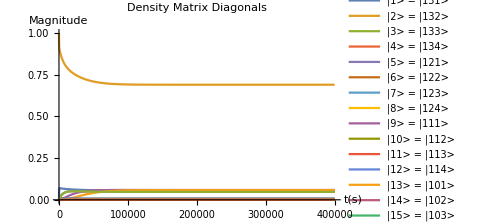
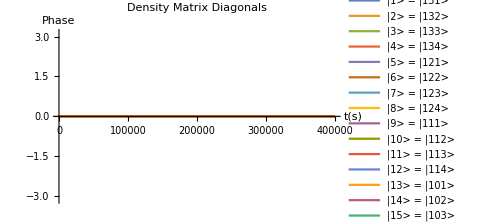

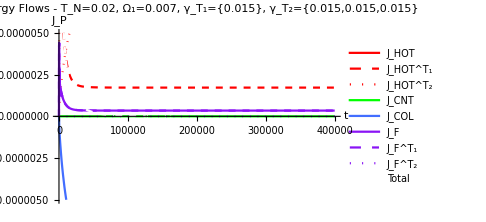

```mathematica
tmax=(400000/ωconv)//.Flatten[{unitassum,Tassum}];

dynamics=NDSolve[
Flatten[{sol//.Flatten[{γassum,NBEassum,unitassum,Tassum,Jassum}],Table[Subscript[ρ, i,j][0]==initρMatrix[[i,j]],{i,1,16Ns},{j,1,16Ns}]}]
,Flatten[Table[Subscript[ρ, i,j],{i,1,16Ns},{j,1,16Ns}]],{t,0,tmax}
];

plot1=Flatten[{Table[Abs[Subscript[ρ, i,i][t]],{i,1,16Ns}]}/.dynamics];
plot2=Flatten[{Table[Arg[Subscript[ρ, i,i][t]],{i,1,16Ns}]}/.dynamics];
{Plot[plot1,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Density Matrix Diagonals"],
	PlotRange-> {0,1},
	AxesLabel->{Style["t(s)"],Style["Magnitude"]}, 
	PlotLegends->Table[StringForm["|``> = |``````>",i,EmapT1[i],Ns-EmapED[i],EmapT2[i]],{i,1,16Ns}]
],
Plot[plot2,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Density Matrix Diagonals"],
	PlotRange-> {-π,π},
	AxesLabel->{Style["t(s)"],Style["Phase"]}, 
	PlotLegends->Table[StringForm["|``> = |``````>",i,EmapT1[i],Ns-EmapED[i],EmapT2[i]],{i,1,16Ns}]
]}

Flatten[{
Subscript[EngyFlowIn, 1,1][ρMatrix[t]]+Subscript[EngyFlowIn, 1,2][ρMatrix[t]],Subscript[EngyFlowIn, 1,1][ρMatrix[t]],Subscript[EngyFlowIn, 1,2][ρMatrix[t]],
Subscript[EngyFlowIn, 2][ρMatrix[t]],Subscript[EngyFlowIn, 3][ρMatrix[t]],
Subscript[EngyFlowIn, 4,1][ρMatrix[t]]+Subscript[EngyFlowIn, 4,2][ρMatrix[t]],Subscript[EngyFlowIn, 4,1][ρMatrix[t]],Subscript[EngyFlowIn, 4,2][ρMatrix[t]],
Subscript[EngyFlowIn, 1,1][ρMatrix[t]]+Subscript[EngyFlowIn, 1,2][ρMatrix[t]]+Subscript[EngyFlowIn, 2][ρMatrix[t]]+Subscript[EngyFlowIn, 3][ρMatrix[t]]+Subscript[EngyFlowIn, 4,1][ρMatrix[t]]+Subscript[EngyFlowIn, 4,2][ρMatrix[t]]}//.Flatten[{γassum,NBEassum,unitassum,Tassum,Jassum}]/.dynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style[StringForm["Energy Flows - T_N=``, Ω_1=``, 
γ_T_1=``, γ_T_2=``",Subscript[T, 2],Subscript[Ω, 1],Table[γT1[i],{i,0,Ns-1-p}],Table[γT2[i],{i,0,Ns-1-q}]]/.Flatten[{γassum,Tassum}]],
	PlotRange->{Automatic, {-0.5 10^-3 Econv Subscript[κ, 1]/.Tassum,0.5 10^-3 Econv Subscript[κ, 1]/.Tassum}},
	AxesLabel->{"t","J_P"},
	PlotLegends->{"J_HOT","J_HOT^T_1","J_HOT^T_2","J_CNT","J_COL","J_F","J_F^T_1","J_F^T_2","Total"},
	PlotStyle->{Red,{Red,Dashed},{Red,Dotted},Green,BlueC,PurpleC,{PurpleC,Dashed},{PurpleC,Dotted},{White,Dashed}}]
```

## Density matrices of the subsystems

Functions for taking the partial trace for the different subsystems. Here nL, nM, nR are the dimensionalities of the respective subsystems.

```mathematica
PartialTraceT1[ρ_,nL_,nM_,nR_]:=Module[{temp0},
Table[
Tr[ArrayReshape[Pick[ρ,Table[a,EmapT1[i]b,EmapT1[j],{i,1,nL nM nR},{j,1,nL nM nR}],1],{(nL nM nR)/nL,(nL nM nR)/nL}]]
,{a,1,nL},{b,1,nL}]
]
PartialTraceED[ρ_,nL_,nM_,nR_]:=Module[{temp0},
Table[
Tr[ArrayReshape[Pick[ρ,Table[a,EmapED[i]b,EmapED[j],{i,1,nL nM nR},{j,1,nL nM nR}],1],{(nL nM nR)/nM,(nL nM nR)/nM}]]
,{a,1,nM},{b,1,nM}]
]
PartialTraceT2[ρ_,nL_,nM_,nR_]:=Module[{temp0},
Table[
Tr[ArrayReshape[Pick[ρ,Table[a,EmapT2[i]b,EmapT2[j],{i,1,nL nM nR},{j,1,nL nM nR}],1],{(nL nM nR)/nR,(nL nM nR)/nR}]]
,{a,1,nR},{b,1,nR}]
]
```

```mathematica
PartialTraceT1[ρMatrix[t],4,Ns,4]//MatrixForm
PartialTraceED[ρMatrix[t],4,Ns,4]//MatrixForm
PartialTraceT2[ρMatrix[t],4,Ns,4]//MatrixForm
```

(ρ_(1,1)[t]+ρ_(2,2)[t]+ρ_(3,3)[t]+ρ_(4,4)[t]+ρ_(5,5)[t]+ρ_(6,6)[t]+ρ_(7,7)[t]+ρ_(8,8)[t]+ρ_(9,9)[t]+ρ_(10,10)[t]+ρ_(11,11)[t]+ρ_(12,12)[t]+ρ_(13,13)[t]+ρ_(14,14)[t]+ρ_(15,15)[t]+ρ_(16,16)[t] | ρ_(1,17)[t]+ρ_(2,18)[t]+ρ_(3,19)[t]+ρ_(4,20)[t]+ρ_(5,21)[t]+ρ_(6,22)[t]+ρ_(7,23)[t]+ρ_(8,24)[t]+ρ_(9,25)[t]+ρ_(10,26)[t]+ρ_(11,27)[t]+ρ_(12,28)[t]+ρ_(13,29)[t]+ρ_(14,30)[t]+ρ_(15,31)[t]+ρ_(16,32)[t] | ρ_(1,33)[t]+ρ_(2,34)[t]+ρ_(3,35)[t]+ρ_(4,36)[t]+ρ_(5,37)[t]+ρ_(6,38)[t]+ρ_(7,39)[t]+ρ_(8,40)[t]+ρ_(9,41)[t]+ρ_(10,42)[t]+ρ_(11,43)[t]+ρ_(12,44)[t]+ρ_(13,45)[t]+ρ_(14,46)[t]+ρ_(15,47)[t]+ρ_(16,48)[t] | ρ_(1,49)[t]+ρ_(2,50)[t]+ρ_(3,51)[t]+ρ_(4,52)[t]+ρ_(5,53)[t]+ρ_(6,54)[t]+ρ_(7,55)[t]+ρ_(8,56)[t]+ρ_(9,57)[t]+ρ_(10,58)[t]+ρ_(11,59)[t]+ρ_(12,60)[t]+ρ_(13,61)[t]+ρ_(14,62)[t]+ρ_(15,63)[t]+ρ_(16,64)[t]
ρ_(17,1)[t]+ρ_(18,2)[t]+ρ_(19,3)[t]+ρ_(20,4)[t]+ρ_(21,5)[t]+ρ_(22,6)[t]+ρ_(23,7)[t]+ρ_(24,8)[t]+ρ_(25,9)[t]+ρ_(26,10)[t]+ρ_(27,11)[t]+ρ_(28,12)[t]+ρ_(29,13)[t]+ρ_(30,14)[t]+ρ_(31,15)[t]+ρ_(32,16)[t] | ρ_(17,17)[t]+ρ_(18,18)[t]+ρ_(19,19)[t]+ρ_(20,20)[t]+ρ_(21,21)[t]+ρ_(22,22)[t]+ρ_(23,23)[t]+ρ_(24,24)[t]+ρ_(25,25)[t]+ρ_(26,26)[t]+ρ_(27,27)[t]+ρ_(28,28)[t]+ρ_(29,29)[t]+ρ_(30,30)[t]+ρ_(31,31)[t]+ρ_(32,32)[t] | ρ_(17,33)[t]+ρ_(18,34)[t]+ρ_(19,35)[t]+ρ_(20,36)[t]+ρ_(21,37)[t]+ρ_(22,38)[t]+ρ_(23,39)[t]+ρ_(24,40)[t]+ρ_(25,41)[t]+ρ_(26,42)[t]+ρ_(27,43)[t]+ρ_(28,44)[t]+ρ_(29,45)[t]+ρ_(30,46)[t]+ρ_(31,47)[t]+ρ_(32,48)[t] | ρ_(17,49)[t]+ρ_(18,50)[t]+ρ_(19,51)[t]+ρ_(20,52)[t]+ρ_(21,53)[t]+ρ_(22,54)[t]+ρ_(23,55)[t]+ρ_(24,56)[t]+ρ_(25,57)[t]+ρ_(26,58)[t]+ρ_(27,59)[t]+ρ_(28,60)[t]+ρ_(29,61)[t]+ρ_(30,62)[t]+ρ_(31,63)[t]+ρ_(32,64)[t]
ρ_(33,1)[t]+ρ_(34,2)[t]+ρ_(35,3)[t]+ρ_(36,4)[t]+ρ_(37,5)[t]+ρ_(38,6)[t]+ρ_(39,7)[t]+ρ_(40,8)[t]+ρ_(41,9)[t]+ρ_(42,10)[t]+ρ_(43,11)[t]+ρ_(44,12)[t]+ρ_(45,13)[t]+ρ_(46,14)[t]+ρ_(47,15)[t]+ρ_(48,16)[t] | ρ_(33,17)[t]+ρ_(34,18)[t]+ρ_(35,19)[t]+ρ_(36,20)[t]+ρ_(37,21)[t]+ρ_(38,22)[t]+ρ_(39,23)[t]+ρ_(40,24)[t]+ρ_(41,25)[t]+ρ_(42,26)[t]+ρ_(43,27)[t]+ρ_(44,28)[t]+ρ_(45,29)[t]+ρ_(46,30)[t]+ρ_(47,31)[t]+ρ_(48,32)[t] | ρ_(33,33)[t]+ρ_(34,34)[t]+ρ_(35,35)[t]+ρ_(36,36)[t]+ρ_(37,37)[t]+ρ_(38,38)[t]+ρ_(39,39)[t]+ρ_(40,40)[t]+ρ_(41,41)[t]+ρ_(42,42)[t]+ρ_(43,43)[t]+ρ_(44,44)[t]+ρ_(45,45)[t]+ρ_(46,46)[t]+ρ_(47,47)[t]+ρ_(48,48)[t] | ρ_(33,49)[t]+ρ_(34,50)[t]+ρ_(35,51)[t]+ρ_(36,52)[t]+ρ_(37,53)[t]+ρ_(38,54)[t]+ρ_(39,55)[t]+ρ_(40,56)[t]+ρ_(41,57)[t]+ρ_(42,58)[t]+ρ_(43,59)[t]+ρ_(44,60)[t]+ρ_(45,61)[t]+ρ_(46,62)[t]+ρ_(47,63)[t]+ρ_(48,64)[t]
ρ_(49,1)[t]+ρ_(50,2)[t]+ρ_(51,3)[t]+ρ_(52,4)[t]+ρ_(53,5)[t]+ρ_(54,6)[t]+ρ_(55,7)[t]+ρ_(56,8)[t]+ρ_(57,9)[t]+ρ_(58,10)[t]+ρ_(59,11)[t]+ρ_(60,12)[t]+ρ_(61,13)[t]+ρ_(62,14)[t]+ρ_(63,15)[t]+ρ_(64,16)[t] | ρ_(49,17)[t]+ρ_(50,18)[t]+ρ_(51,19)[t]+ρ_(52,20)[t]+ρ_(53,21)[t]+ρ_(54,22)[t]+ρ_(55,23)[t]+ρ_(56,24)[t]+ρ_(57,25)[t]+ρ_(58,26)[t]+ρ_(59,27)[t]+ρ_(60,28)[t]+ρ_(61,29)[t]+ρ_(62,30)[t]+ρ_(63,31)[t]+ρ_(64,32)[t] | ρ_(49,33)[t]+ρ_(50,34)[t]+ρ_(51,35)[t]+ρ_(52,36)[t]+ρ_(53,37)[t]+ρ_(54,38)[t]+ρ_(55,39)[t]+ρ_(56,40)[t]+ρ_(57,41)[t]+ρ_(58,42)[t]+ρ_(59,43)[t]+ρ_(60,44)[t]+ρ_(61,45)[t]+ρ_(62,46)[t]+ρ_(63,47)[t]+ρ_(64,48)[t] | ρ_(49,49)[t]+ρ_(50,50)[t]+ρ_(51,51)[t]+ρ_(52,52)[t]+ρ_(53,53)[t]+ρ_(54,54)[t]+ρ_(55,55)[t]+ρ_(56,56)[t]+ρ_(57,57)[t]+ρ_(58,58)[t]+ρ_(59,59)[t]+ρ_(60,60)[t]+ρ_(61,61)[t]+ρ_(62,62)[t]+ρ_(63,63)[t]+ρ_(64,64)[t])

(ρ_(1,1)[t]+ρ_(2,2)[t]+ρ_(3,3)[t]+ρ_(4,4)[t]+ρ_(17,17)[t]+ρ_(18,18)[t]+ρ_(19,19)[t]+ρ_(20,20)[t]+ρ_(33,33)[t]+ρ_(34,34)[t]+ρ_(35,35)[t]+ρ_(36,36)[t]+ρ_(49,49)[t]+ρ_(50,50)[t]+ρ_(51,51)[t]+ρ_(52,52)[t] | ρ_(1,5)[t]+ρ_(2,6)[t]+ρ_(3,7)[t]+ρ_(4,8)[t]+ρ_(17,21)[t]+ρ_(18,22)[t]+ρ_(19,23)[t]+ρ_(20,24)[t]+ρ_(33,37)[t]+ρ_(34,38)[t]+ρ_(35,39)[t]+ρ_(36,40)[t]+ρ_(49,53)[t]+ρ_(50,54)[t]+ρ_(51,55)[t]+ρ_(52,56)[t] | ρ_(1,9)[t]+ρ_(2,10)[t]+ρ_(3,11)[t]+ρ_(4,12)[t]+ρ_(17,25)[t]+ρ_(18,26)[t]+ρ_(19,27)[t]+ρ_(20,28)[t]+ρ_(33,41)[t]+ρ_(34,42)[t]+ρ_(35,43)[t]+ρ_(36,44)[t]+ρ_(49,57)[t]+ρ_(50,58)[t]+ρ_(51,59)[t]+ρ_(52,60)[t] | ρ_(1,13)[t]+ρ_(2,14)[t]+ρ_(3,15)[t]+ρ_(4,16)[t]+ρ_(17,29)[t]+ρ_(18,30)[t]+ρ_(19,31)[t]+ρ_(20,32)[t]+ρ_(33,45)[t]+ρ_(34,46)[t]+ρ_(35,47)[t]+ρ_(36,48)[t]+ρ_(49,61)[t]+ρ_(50,62)[t]+ρ_(51,63)[t]+ρ_(52,64)[t]
ρ_(5,1)[t]+ρ_(6,2)[t]+ρ_(7,3)[t]+ρ_(8,4)[t]+ρ_(21,17)[t]+ρ_(22,18)[t]+ρ_(23,19)[t]+ρ_(24,20)[t]+ρ_(37,33)[t]+ρ_(38,34)[t]+ρ_(39,35)[t]+ρ_(40,36)[t]+ρ_(53,49)[t]+ρ_(54,50)[t]+ρ_(55,51)[t]+ρ_(56,52)[t] | ρ_(5,5)[t]+ρ_(6,6)[t]+ρ_(7,7)[t]+ρ_(8,8)[t]+ρ_(21,21)[t]+ρ_(22,22)[t]+ρ_(23,23)[t]+ρ_(24,24)[t]+ρ_(37,37)[t]+ρ_(38,38)[t]+ρ_(39,39)[t]+ρ_(40,40)[t]+ρ_(53,53)[t]+ρ_(54,54)[t]+ρ_(55,55)[t]+ρ_(56,56)[t] | ρ_(5,9)[t]+ρ_(6,10)[t]+ρ_(7,11)[t]+ρ_(8,12)[t]+ρ_(21,25)[t]+ρ_(22,26)[t]+ρ_(23,27)[t]+ρ_(24,28)[t]+ρ_(37,41)[t]+ρ_(38,42)[t]+ρ_(39,43)[t]+ρ_(40,44)[t]+ρ_(53,57)[t]+ρ_(54,58)[t]+ρ_(55,59)[t]+ρ_(56,60)[t] | ρ_(5,13)[t]+ρ_(6,14)[t]+ρ_(7,15)[t]+ρ_(8,16)[t]+ρ_(21,29)[t]+ρ_(22,30)[t]+ρ_(23,31)[t]+ρ_(24,32)[t]+ρ_(37,45)[t]+ρ_(38,46)[t]+ρ_(39,47)[t]+ρ_(40,48)[t]+ρ_(53,61)[t]+ρ_(54,62)[t]+ρ_(55,63)[t]+ρ_(56,64)[t]
ρ_(9,1)[t]+ρ_(10,2)[t]+ρ_(11,3)[t]+ρ_(12,4)[t]+ρ_(25,17)[t]+ρ_(26,18)[t]+ρ_(27,19)[t]+ρ_(28,20)[t]+ρ_(41,33)[t]+ρ_(42,34)[t]+ρ_(43,35)[t]+ρ_(44,36)[t]+ρ_(57,49)[t]+ρ_(58,50)[t]+ρ_(59,51)[t]+ρ_(60,52)[t] | ρ_(9,5)[t]+ρ_(10,6)[t]+ρ_(11,7)[t]+ρ_(12,8)[t]+ρ_(25,21)[t]+ρ_(26,22)[t]+ρ_(27,23)[t]+ρ_(28,24)[t]+ρ_(41,37)[t]+ρ_(42,38)[t]+ρ_(43,39)[t]+ρ_(44,40)[t]+ρ_(57,53)[t]+ρ_(58,54)[t]+ρ_(59,55)[t]+ρ_(60,56)[t] | ρ_(9,9)[t]+ρ_(10,10)[t]+ρ_(11,11)[t]+ρ_(12,12)[t]+ρ_(25,25)[t]+ρ_(26,26)[t]+ρ_(27,27)[t]+ρ_(28,28)[t]+ρ_(41,41)[t]+ρ_(42,42)[t]+ρ_(43,43)[t]+ρ_(44,44)[t]+ρ_(57,57)[t]+ρ_(58,58)[t]+ρ_(59,59)[t]+ρ_(60,60)[t] | ρ_(9,13)[t]+ρ_(10,14)[t]+ρ_(11,15)[t]+ρ_(12,16)[t]+ρ_(25,29)[t]+ρ_(26,30)[t]+ρ_(27,31)[t]+ρ_(28,32)[t]+ρ_(41,45)[t]+ρ_(42,46)[t]+ρ_(43,47)[t]+ρ_(44,48)[t]+ρ_(57,61)[t]+ρ_(58,62)[t]+ρ_(59,63)[t]+ρ_(60,64)[t]
ρ_(13,1)[t]+ρ_(14,2)[t]+ρ_(15,3)[t]+ρ_(16,4)[t]+ρ_(29,17)[t]+ρ_(30,18)[t]+ρ_(31,19)[t]+ρ_(32,20)[t]+ρ_(45,33)[t]+ρ_(46,34)[t]+ρ_(47,35)[t]+ρ_(48,36)[t]+ρ_(61,49)[t]+ρ_(62,50)[t]+ρ_(63,51)[t]+ρ_(64,52)[t] | ρ_(13,5)[t]+ρ_(14,6)[t]+ρ_(15,7)[t]+ρ_(16,8)[t]+ρ_(29,21)[t]+ρ_(30,22)[t]+ρ_(31,23)[t]+ρ_(32,24)[t]+ρ_(45,37)[t]+ρ_(46,38)[t]+ρ_(47,39)[t]+ρ_(48,40)[t]+ρ_(61,53)[t]+ρ_(62,54)[t]+ρ_(63,55)[t]+ρ_(64,56)[t] | ρ_(13,9)[t]+ρ_(14,10)[t]+ρ_(15,11)[t]+ρ_(16,12)[t]+ρ_(29,25)[t]+ρ_(30,26)[t]+ρ_(31,27)[t]+ρ_(32,28)[t]+ρ_(45,41)[t]+ρ_(46,42)[t]+ρ_(47,43)[t]+ρ_(48,44)[t]+ρ_(61,57)[t]+ρ_(62,58)[t]+ρ_(63,59)[t]+ρ_(64,60)[t] | ρ_(13,13)[t]+ρ_(14,14)[t]+ρ_(15,15)[t]+ρ_(16,16)[t]+ρ_(29,29)[t]+ρ_(30,30)[t]+ρ_(31,31)[t]+ρ_(32,32)[t]+ρ_(45,45)[t]+ρ_(46,46)[t]+ρ_(47,47)[t]+ρ_(48,48)[t]+ρ_(61,61)[t]+ρ_(62,62)[t]+ρ_(63,63)[t]+ρ_(64,64)[t])

(ρ_(1,1)[t]+ρ_(5,5)[t]+ρ_(9,9)[t]+ρ_(13,13)[t]+ρ_(17,17)[t]+ρ_(21,21)[t]+ρ_(25,25)[t]+ρ_(29,29)[t]+ρ_(33,33)[t]+ρ_(37,37)[t]+ρ_(41,41)[t]+ρ_(45,45)[t]+ρ_(49,49)[t]+ρ_(53,53)[t]+ρ_(57,57)[t]+ρ_(61,61)[t] | ρ_(1,2)[t]+ρ_(5,6)[t]+ρ_(9,10)[t]+ρ_(13,14)[t]+ρ_(17,18)[t]+ρ_(21,22)[t]+ρ_(25,26)[t]+ρ_(29,30)[t]+ρ_(33,34)[t]+ρ_(37,38)[t]+ρ_(41,42)[t]+ρ_(45,46)[t]+ρ_(49,50)[t]+ρ_(53,54)[t]+ρ_(57,58)[t]+ρ_(61,62)[t] | ρ_(1,3)[t]+ρ_(5,7)[t]+ρ_(9,11)[t]+ρ_(13,15)[t]+ρ_(17,19)[t]+ρ_(21,23)[t]+ρ_(25,27)[t]+ρ_(29,31)[t]+ρ_(33,35)[t]+ρ_(37,39)[t]+ρ_(41,43)[t]+ρ_(45,47)[t]+ρ_(49,51)[t]+ρ_(53,55)[t]+ρ_(57,59)[t]+ρ_(61,63)[t] | ρ_(1,4)[t]+ρ_(5,8)[t]+ρ_(9,12)[t]+ρ_(13,16)[t]+ρ_(17,20)[t]+ρ_(21,24)[t]+ρ_(25,28)[t]+ρ_(29,32)[t]+ρ_(33,36)[t]+ρ_(37,40)[t]+ρ_(41,44)[t]+ρ_(45,48)[t]+ρ_(49,52)[t]+ρ_(53,56)[t]+ρ_(57,60)[t]+ρ_(61,64)[t]
ρ_(2,1)[t]+ρ_(6,5)[t]+ρ_(10,9)[t]+ρ_(14,13)[t]+ρ_(18,17)[t]+ρ_(22,21)[t]+ρ_(26,25)[t]+ρ_(30,29)[t]+ρ_(34,33)[t]+ρ_(38,37)[t]+ρ_(42,41)[t]+ρ_(46,45)[t]+ρ_(50,49)[t]+ρ_(54,53)[t]+ρ_(58,57)[t]+ρ_(62,61)[t] | ρ_(2,2)[t]+ρ_(6,6)[t]+ρ_(10,10)[t]+ρ_(14,14)[t]+ρ_(18,18)[t]+ρ_(22,22)[t]+ρ_(26,26)[t]+ρ_(30,30)[t]+ρ_(34,34)[t]+ρ_(38,38)[t]+ρ_(42,42)[t]+ρ_(46,46)[t]+ρ_(50,50)[t]+ρ_(54,54)[t]+ρ_(58,58)[t]+ρ_(62,62)[t] | ρ_(2,3)[t]+ρ_(6,7)[t]+ρ_(10,11)[t]+ρ_(14,15)[t]+ρ_(18,19)[t]+ρ_(22,23)[t]+ρ_(26,27)[t]+ρ_(30,31)[t]+ρ_(34,35)[t]+ρ_(38,39)[t]+ρ_(42,43)[t]+ρ_(46,47)[t]+ρ_(50,51)[t]+ρ_(54,55)[t]+ρ_(58,59)[t]+ρ_(62,63)[t] | ρ_(2,4)[t]+ρ_(6,8)[t]+ρ_(10,12)[t]+ρ_(14,16)[t]+ρ_(18,20)[t]+ρ_(22,24)[t]+ρ_(26,28)[t]+ρ_(30,32)[t]+ρ_(34,36)[t]+ρ_(38,40)[t]+ρ_(42,44)[t]+ρ_(46,48)[t]+ρ_(50,52)[t]+ρ_(54,56)[t]+ρ_(58,60)[t]+ρ_(62,64)[t]
ρ_(3,1)[t]+ρ_(7,5)[t]+ρ_(11,9)[t]+ρ_(15,13)[t]+ρ_(19,17)[t]+ρ_(23,21)[t]+ρ_(27,25)[t]+ρ_(31,29)[t]+ρ_(35,33)[t]+ρ_(39,37)[t]+ρ_(43,41)[t]+ρ_(47,45)[t]+ρ_(51,49)[t]+ρ_(55,53)[t]+ρ_(59,57)[t]+ρ_(63,61)[t] | ρ_(3,2)[t]+ρ_(7,6)[t]+ρ_(11,10)[t]+ρ_(15,14)[t]+ρ_(19,18)[t]+ρ_(23,22)[t]+ρ_(27,26)[t]+ρ_(31,30)[t]+ρ_(35,34)[t]+ρ_(39,38)[t]+ρ_(43,42)[t]+ρ_(47,46)[t]+ρ_(51,50)[t]+ρ_(55,54)[t]+ρ_(59,58)[t]+ρ_(63,62)[t] | ρ_(3,3)[t]+ρ_(7,7)[t]+ρ_(11,11)[t]+ρ_(15,15)[t]+ρ_(19,19)[t]+ρ_(23,23)[t]+ρ_(27,27)[t]+ρ_(31,31)[t]+ρ_(35,35)[t]+ρ_(39,39)[t]+ρ_(43,43)[t]+ρ_(47,47)[t]+ρ_(51,51)[t]+ρ_(55,55)[t]+ρ_(59,59)[t]+ρ_(63,63)[t] | ρ_(3,4)[t]+ρ_(7,8)[t]+ρ_(11,12)[t]+ρ_(15,16)[t]+ρ_(19,20)[t]+ρ_(23,24)[t]+ρ_(27,28)[t]+ρ_(31,32)[t]+ρ_(35,36)[t]+ρ_(39,40)[t]+ρ_(43,44)[t]+ρ_(47,48)[t]+ρ_(51,52)[t]+ρ_(55,56)[t]+ρ_(59,60)[t]+ρ_(63,64)[t]
ρ_(4,1)[t]+ρ_(8,5)[t]+ρ_(12,9)[t]+ρ_(16,13)[t]+ρ_(20,17)[t]+ρ_(24,21)[t]+ρ_(28,25)[t]+ρ_(32,29)[t]+ρ_(36,33)[t]+ρ_(40,37)[t]+ρ_(44,41)[t]+ρ_(48,45)[t]+ρ_(52,49)[t]+ρ_(56,53)[t]+ρ_(60,57)[t]+ρ_(64,61)[t] | ρ_(4,2)[t]+ρ_(8,6)[t]+ρ_(12,10)[t]+ρ_(16,14)[t]+ρ_(20,18)[t]+ρ_(24,22)[t]+ρ_(28,26)[t]+ρ_(32,30)[t]+ρ_(36,34)[t]+ρ_(40,38)[t]+ρ_(44,42)[t]+ρ_(48,46)[t]+ρ_(52,50)[t]+ρ_(56,54)[t]+ρ_(60,58)[t]+ρ_(64,62)[t] | ρ_(4,3)[t]+ρ_(8,7)[t]+ρ_(12,11)[t]+ρ_(16,15)[t]+ρ_(20,19)[t]+ρ_(24,23)[t]+ρ_(28,27)[t]+ρ_(32,31)[t]+ρ_(36,35)[t]+ρ_(40,39)[t]+ρ_(44,43)[t]+ρ_(48,47)[t]+ρ_(52,51)[t]+ρ_(56,55)[t]+ρ_(60,59)[t]+ρ_(64,63)[t] | ρ_(4,4)[t]+ρ_(8,8)[t]+ρ_(12,12)[t]+ρ_(16,16)[t]+ρ_(20,20)[t]+ρ_(24,24)[t]+ρ_(28,28)[t]+ρ_(32,32)[t]+ρ_(36,36)[t]+ρ_(40,40)[t]+ρ_(44,44)[t]+ρ_(48,48)[t]+ρ_(52,52)[t]+ρ_(56,56)[t]+ρ_(60,60)[t]+ρ_(64,64)[t])

## Numerically obtaining the approximate steady-state

Because ParallelTable doesn’t work properly with EngyFlowIn_P[ρ], we need to redefine them

```mathematica
EngyFlowInHT1=Subscript[EngyFlowIn, 1,1][ρMatrix[t]];
EngyFlowInHT2=Subscript[EngyFlowIn, 1,2][ρMatrix[t]];
EngyFlowInN=Subscript[EngyFlowIn, 2][ρMatrix[t]];
EngyFlowInC=Subscript[EngyFlowIn, 3][ρMatrix[t]];
EngyFlowInFT1=Subscript[EngyFlowIn, 4,1][ρMatrix[t]];
EngyFlowInFT2=Subscript[EngyFlowIn, 4,2][ρMatrix[t]];
```

```mathematica
varFunc[T1_,T2_,T3_,κ1_,κ2_,κ3_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,ωEDs_,Ω1_,Ω2_,γT1s_,γT2s_,tmax_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{unitassum,NBEassum,Jassum,Subscript[T, 1]->T1,Subscript[T, 2]->T2,Subscript[T, 3]->T3,Subscript[κ, 1]->κ1,Subscript[κ, 2]->κ2,Subscript[κ, 3]->κ3,Subscript[Ω, 1]->Ω1,Subscript[Ω, 2]->Ω2,Subscript[ωLM, 1]->ωLM1,Subscript[ωMR, 1]->ωMR1,Subscript[ωLM, 2]->ωLM2,Subscript[ωMR, 2]->ωMR2,ωED->ωEDs,Table[γT1[i]->γT1s[[i+1]],{i,0,Ns-1-p}],Table[γT2[i]->γT2s[[i+1]],{i,0,Ns-1-q}]}];
temp1=sol//.temp0;
temp2=NDSolve[
Flatten[{temp1,Table[Subscript[ρ, i,j][0]==i,j i,groundstate 1,{i,1,16Ns},{j,1,16Ns}]}],Flatten[Table[Subscript[ρ, i,j],{i,1,16Ns},{j,1,16Ns}]],{t,0,tmax}];
temp3=Table[Subscript[ρ, i,j][tmax],{i,1,16Ns},{j,1,16Ns}]//.Flatten[temp2];
{
Re[Flatten[Table[Subscript[ρ, i,i][tmax],{i,1,16Ns}]/.temp2]],
Re[Flatten[{
EngyFlowInHT1+EngyFlowInHT2,EngyFlowInHT1,EngyFlowInHT2,EngyFlowInN,EngyFlowInC,
EngyFlowInFT1+EngyFlowInFT2}//.Flatten[{t->tmax,temp0}]/.temp2]],
Table[Subscript[ρ, i,j][tmax],{i,1,16Ns},{j,1,16Ns}]/.temp2
}
]
```

```mathematica
varFunc[0.2,0.1,0.02,0.01,0.001,0.01,0.5,0.6,0.9,1.1,0.2,0.0,0.0,ConstantArray[0.015ωconv,Ns-p],ConstantArray[0.015ωconv,Ns-q],1000000,unitassum][[1;;2]]//AbsoluteTiming
```

{46.1849,{{7.55565×10^-14,7.91464×10^-8,0.0000139559,8.37392×10^-12,3.21433×10^-10,1.18772×10^-7,0.0000210335,6.36062×10^-8,4.79302×10^-10,1.06389×10^-7,0.0000217203,9.52164×10^-8,2.5161×10^-10,7.78693×10^-6,0.00099588,5.78261×10^-8,3.39991×10^-10,7.92375×10^-6,0.00100332,5.76563×10^-8,2.86239×10^-8,7.45734×10^-6,0.00132123,5.59892×10^-6,3.00566×10^-8,7.43252×10^-6,0.00131777,5.97527×10^-6,2.99255×10^-8,0.000774813,0.0697982,5.95364×10^-6,5.02336×10^-9,0.000109468,0.0134829,8.9035×10^-7,3.71546×10^-7,0.0000912484,0.0161681,0.0000739667,3.67694×10^-7,0.0000909298,0.0161124,0.000073105,3.66393×10^-7,0.00949143,0.854499,0.0000728501,2.40317×10^-12,1.16979×10^-6,0.000205343,2.92399×10^-10,4.75914×10^-9,1.73973×10^-6,0.000308096,9.40893×10^-7,7.02045×10^-9,1.55442×10^-6,0.000317785,1.39468×10^-6,3.31441×10^-9,0.000102087,0.0134746,7.60291×10^-7},{4.00062×10^-6,1.59565×10^-6,2.40497×10^-6,-1.06121×10^-6,-2.93941×10^-6,0.}}}

```mathematica
varFunc[T1_,T2_,T3_,κ1_,κ2_,κ3_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,ωEDs_,Ω1_,Ω2_,γT1s_,γT2s_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{unitassum,NBEassum,Jassum,Subscript[T, 1]->T1,Subscript[T, 2]->T2,Subscript[T, 3]->T3,Subscript[κ, 1]->κ1,Subscript[κ, 2]->κ2,Subscript[κ, 3]->κ3,Subscript[Ω, 1]->Ω1,Subscript[Ω, 2]->Ω2,Subscript[ωLM, 1]->ωLM1,Subscript[ωMR, 1]->ωMR1,Subscript[ωLM, 2]->ωLM2,Subscript[ωMR, 2]->ωMR2,ωED->ωEDs,Table[γT1[i]->γT1s[[i+1]],{i,0,Ns-1-p}],Table[γT2[i]->γT2s[[i+1]],{i,0,Ns-1-q}]}];
temp1=sol//.temp0;
temp2=NSolve[Flatten[{temp1//.{Subscript[ρ, i_,j_]'[t]->0,Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j]},∑_(i=1)^(16 Ns) Subscript[ρ, i,i]==1}],Flatten[Table[Subscript[ρ, i,j],{i,1,16Ns},{j,1,16Ns}]]];
temp3=Table[Subscript[ρ, i,j],{i,1,16Ns},{j,1,16Ns}]//.Flatten[temp2];
{
Re[Flatten[Table[Subscript[ρ, i,i],{i,1,16Ns}]/.temp2]],
Re[Flatten[{
EngyFlowInHT1+EngyFlowInHT2,EngyFlowInHT1,EngyFlowInHT2,EngyFlowInN,EngyFlowInC,
EngyFlowInFT1+EngyFlowInFT2}//.Flatten[{Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j],temp0}]/.temp2]],
PartialTraceT1[temp3,4,Ns,4],
PartialTraceED[temp3,4,Ns,4],
PartialTraceT2[temp3,4,Ns,4],
Diagonal[Re[PartialTraceT1[temp3,4,Ns,4]]],
Diagonal[Re[PartialTraceED[temp3,4,Ns,4]]],
Diagonal[Re[PartialTraceT2[temp3,4,Ns,4]]]
}
]
```

```mathematica
varFunc[0.2,0.1,0.02,0.01,0.001,0.01,0.5,0.6,0.9,1.1,0.2,0.0,0.0,ConstantArray[0.015ωconv,Ns-p],ConstantArray[0.015ωconv,Ns-q],unitassum][[1;;2]]//AbsoluteTiming
```

{5.05918,{{7.55568×10^-14,7.91464×10^-8,0.0000139559,8.37388×10^-12,3.21433×10^-10,1.18772×10^-7,0.0000210335,6.36062×10^-8,4.79302×10^-10,1.06389×10^-7,0.0000217203,9.52164×10^-8,2.5161×10^-10,7.78693×10^-6,0.00099588,5.78261×10^-8,3.39991×10^-10,7.92375×10^-6,0.00100332,5.76563×10^-8,2.86239×10^-8,7.45734×10^-6,0.00132123,5.59892×10^-6,3.00566×10^-8,7.43252×10^-6,0.00131777,5.97527×10^-6,2.99255×10^-8,0.000774813,0.0697982,5.95364×10^-6,5.02336×10^-9,0.000109468,0.0134829,8.9035×10^-7,3.71546×10^-7,0.0000912484,0.0161681,0.0000739667,3.67694×10^-7,0.0000909298,0.0161125,0.000073105,3.66393×10^-7,0.00949143,0.854499,0.0000728501,2.40317×10^-12,1.16979×10^-6,0.000205343,2.92399×10^-10,4.75914×10^-9,1.73973×10^-6,0.000308096,9.40893×10^-7,7.02044×10^-9,1.55442×10^-6,0.000317785,1.39468×10^-6,3.31441×10^-9,0.000102087,0.0134746,7.60291×10^-7},{4.00062×10^-6,1.59565×10^-6,2.40497×10^-6,-1.06121×10^-6,-2.93941×10^-6,0.}}}

Some example configurations

{4.00062×10^-6,1.59565×10^-6,2.40497×10^-6,-1.06121×10^-6,-2.93941×10^-6,0.}

{(0.0010609+0. ⅈ | 0 | 0 | 0
0 | 0.0742559+0. ⅈ | 0 | 0
0 | 0 | 0.910268+0. ⅈ | 0
0 | 0 | 0 | 0.0144155+0. ⅈ),(0.0148251+0. ⅈ | 0 | 0 | 0
0 | 0.018+0. ⅈ | 0 | 0
0 | 0 | 0.0179507+0. ⅈ | 0
0 | 0 | 0 | 0.949224+0. ⅈ),(1.21575×10^-6+0. ⅈ | 0 | 0. | 0
0 | 0.0106953+0. ⅈ | 0 | 0
0. | 0 | 0.989062+0. ⅈ | 0
0 | 0 | 0 | 0.00024171+0. ⅈ)}

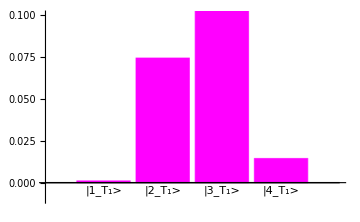
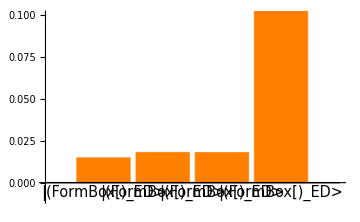
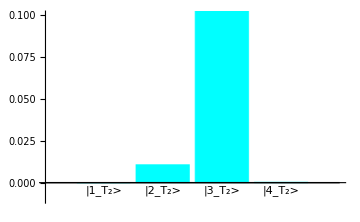

```mathematica
temp=varFunc[0.2,0.1,0.02,0.01,0.001,0.01,0.5,0.6,0.9,1.1,0.2,0.0,0.0,ConstantArray[0.015ωconv,Ns-p],ConstantArray[0.015ωconv,Ns-q],unitassum];
temp[[2]]
{temp[[3]]//MatrixForm,temp[[4]]//MatrixForm,temp[[5]]//MatrixForm}
{BarChart[temp[[6]],ChartLabels->{"|1_T_1>","|2_T_1>","|3_T_1>","|4_T_1>"},ImageSize->Medium,PlotRange->{-0.01,0.1},ChartStyle->Magenta],
BarChart[temp[[7]],ChartLabels->Table[Style[StringForm["|(``)_ED>",Ns-i],FontFamily->"Times New Roman",FontSize->14.5],{i,1,Ns}],ImageSize->Medium,PlotRange->{-0.01,0.1},ChartStyle->Orange],
BarChart[temp[[8]],ChartLabels->{"|1_T_2>","|2_T_2>","|3_T_2>","|4_T_2>"},ImageSize->Medium,PlotRange->{-0.01,0.1},ChartStyle->Cyan]}
```

## Energy flow characteristics for different system parameters

### Energy flow under different control temperatures

Energy flows when ω_2 is changed from below ω_3 to above ω_3, keeping the γs constant,

```mathematica
PlotEngyFlowsWithTcnt[Thot_,Tcol_,κhot_,κcnt_,κcol_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,ωEDs_,Ω1s_,Ω2s_,γT1s_,γT2s_,Tcntmin_,Tcntmax_,Tres_,legends_,title_]:=Module[{tempx,tempy,combflows,denmatT1,denmatED,denmatT2,amplif},
tempx=Table[Tcnt/Thot,{Tcnt,Tcntmin,Tcntmax,Tres},{i,1,9}];
tempy=ParallelTable[varFunc[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω1s,Ω2s,γT1s,γT2s,unitassum],{Tcnt,Tcntmin,Tcntmax,Tres}];
combflows=Table[MapThread[List,{tempx[[;;,i]],10^6 tempy[[;;,2,i]]}],{i,1,5}];
denmatT1=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,6,i]]}],{i,1,4}];
denmatED=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,7,i]]}],{i,1,Ns}];
denmatT2=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,8,i]]}],{i,1,4}];
amplif=MapThread[List,{Drop[tempx[[;;,1]],-1],Differences[tempy[[;;,2,1]]]/Differences[tempy[[;;,2,4]]]}];
{ListPlot[combflows,
PlotRange->{{Tcntmin/Thot,Tcntmax/Thot},Full},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["T_N/T_H",FontFamily->"Times New Roman",FontSize->16],
		Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style[title,FontFamily->"Times New Roman",FontSize->14.5],
PlotStyle->{{Red},{Red,Dashed},{Red,Dotted},{Green},{BlueC}},
PlotLegends->legends &&{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_H1",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_H2",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5]}],
ListLogPlot[denmatT1,
PlotRange->{{Tcntmin/Thot,Tcntmax/Thot},{0.0001,1}},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["T_N/T_H",FontFamily->"Times New Roman",FontSize->16],
		Style["Populations",FontFamily->"Times New Roman",FontSize->16]},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style["T_1 - Density matrix diagonals",FontFamily->"Times New Roman",FontSize->14.5],
PlotLegends->legends &&{
Style["|1_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_1>",FontFamily->"Times New Roman",FontSize->14.5]}],
ListLogPlot[denmatED,
PlotRange->{{Tcntmin/Thot,Tcntmax/Thot},{0.0001,1}},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["T_N/T_H",FontFamily->"Times New Roman",FontSize->16],
		Style["Populations",FontFamily->"Times New Roman",FontSize->16]},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style["ED - Density matrix diagonals",FontFamily->"Times New Roman",FontSize->14.5],
PlotLegends->legends &&Table[Style[StringForm["|(``)_ED>",Ns-i],FontFamily->"Times New Roman",FontSize->14.5],{i,1,Ns}]],
ListLogPlot[denmatT2,
PlotRange->{{Tcntmin/Thot,Tcntmax/Thot},{0.0001,1}},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["T_N/T_H",FontFamily->"Times New Roman",FontSize->16],
		Style["Populations",FontFamily->"Times New Roman",FontSize->16]},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style["T_2 - Density matrix diagonals",FontFamily->"Times New Roman",FontSize->14.5],
PlotLegends->legends &&{
Style["|1_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_2>",FontFamily->"Times New Roman",FontSize->14.5]}],
ListPlot[amplif,
	ImageSize->Medium,
	PlotRange->{{Tcntmin/Thot,Tcntmax/Thot},Automatic},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["T_N/T_H",FontFamily->"Times New Roman",FontSize->15],
		Style["α_Te = ΔJ_H/ΔJ_N",FontFamily->"Times New Roman",FontSize->15]},
	FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},	
	PlotStyle->{Black},
	Joined->True]
}
]
```

### Time domain behaviors

Find the stable density matrix for the initial condition.

```mathematica
findInitMatrix[T1_,T2_,T3_,κ1_,κ2_,κ3_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,ωEDs_,Ω1_,Ω2_,γT1s_,γT2s_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{unitassum,NBEassum,Jassum,Subscript[T, 1]->T1,Subscript[T, 2]->T2,Subscript[T, 3]->T3,Subscript[κ, 1]->κ1,Subscript[κ, 2]->κ2,Subscript[κ, 3]->κ3,Subscript[Ω, 1]->Ω1,Subscript[Ω, 2]->Ω2,Subscript[ωLM, 1]->ωLM1,Subscript[ωMR, 1]->ωMR1,Subscript[ωLM, 2]->ωLM2,Subscript[ωMR, 2]->ωMR2,ωED->ωEDs,Table[γT1[i]->γT1s[[i+1]],{i,0,Ns-1-p}],Table[γT2[i]->γT2s[[i+1]],{i,0,Ns-1-q}]}];
temp1=sol//.temp0;
temp2=NSolve[Flatten[{temp1//.{Subscript[ρ, i_,j_]'[t]->0,Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j]},∑_(i=1)^(16 Ns) Subscript[ρ, i,i]==1}],Flatten[Table[Subscript[ρ, i,j],{i,1,16Ns},{j,1,16Ns}]]];
temp3=Table[Subscript[ρ, i,j],{i,1,16Ns},{j,1,16Ns}]//.Flatten[temp2];
Table[Subscript[ρ, i,j],{i,1,16Ns},{j,1,16Ns}]/.temp2
]
```

Plot time domain

```mathematica
PlotTimeDomainWithT[Thots_,Tcols_,κhots_,κcnts_,κcols_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,Ω1_,Ω2_,ωEDs_,γT1s_,γT2s_, Tcnt1s_,Tcnt2s_,tstart_,tchange_,tmax_]:=Module[{timeassum,sysassum,indsysassum,motioneqs,initMatrix,indmotioneqs,initconditions,indinitconditions,dynamics,inddynamics,tempgraph,denmatS1graph,denmatS2graph,denmatEDgraph,flowgraph,inddenmatgraph,indflowgraph},
timeassum:={
Tcnt-> Piecewise[{{Tcnt1s,t<tchange},{Tcnt2s,t>tchange}}]
};
sysassum =Flatten[ {
Subscript[T, 1]-> Thots,Subscript[T, 2]-> Tcnt,Subscript[T, 3]-> Tcols,
Subscript[κ, 1]->κhots,Subscript[κ, 2]->κcnts,Subscript[κ, 3]->κcols,
Subscript[ωLM, 1]->ωLM1,Subscript[ωMR, 1]->ωMR1,
Subscript[ωLM, 2]->ωLM2,Subscript[ωMR, 2]->ωMR2,
Subscript[Ω, 1]->Ω1,Subscript[Ω, 2]->Ω2,
ωED->ωEDs,
Table[γT1[i]->γT1s[[i+1]],{i,0,Ns-1-p}],Table[γT2[i]->γT2s[[i+1]],{i,0,Ns-1-q}]
}];

initMatrix=findInitMatrix[Thots,Tcnt1s,Tcols,κhots,κcnts,κcols,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω1,Ω2,γT1s,γT2s,unitassum];

motioneqs=sol//.Flatten[{NBEassum,unitassum,timeassum,sysassum,Jassum}];
initconditions={Table[Subscript[ρ, i,j][0]==initMatrix[[1,i,j]],{i,1,16Ns},{j,1,16Ns}]}/.sysassum;

dynamics = NDSolve[
Flatten[{motioneqs,initconditions}]
,Flatten[Table[Subscript[ρ, i,j],{i,1,16Ns},{j,1,16Ns}]],{t,tstart,tmax}
];

denmatS1graph=Flatten[Table[PartialTraceT1[ρMatrix[10^6 t],4,Ns,4][[i,i]],{i,1,4}]/.dynamics];
denmatEDgraph=Flatten[Table[PartialTraceED[ρMatrix[10^6 t],4,Ns,4][[i,i]],{i,1,Ns}]/.dynamics];
denmatS2graph=Flatten[Table[PartialTraceT2[ρMatrix[10^6 t],4,Ns,4][[i,i]],{i,1,4}]/.dynamics];

flowgraph=Re[Flatten[10^6{
Subscript[EngyFlowIn, 1,1][ρMatrix[t]]+Subscript[EngyFlowIn, 1,2][ρMatrix[t]],
Subscript[EngyFlowIn, 2][ρMatrix[t]],Subscript[EngyFlowIn, 3][ρMatrix[t]]}//.Flatten[{NBEassum,unitassum,timeassum,sysassum,Jassum}]/.dynamics]]/.t->10^6 t;

{
timedom=Plot[flowgraph,{t,0,10^-6 tmax},
ImageSize->Medium,
PlotRange->{Automatic, Automatic},
PlotLegends->{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5]},
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]}, 
GridLines->{None,{0}},
PlotStyle->{Red,Green,BlueC,PurpleC}],
LogPlot[denmatS1graph,{t,0,10^-6 tmax},
ImageSize->Medium,
	PlotLabel->  Style["S1 - Density Matrix Diagonals",FontFamily->"Times New Roman",FontSize->14.5],
	PlotRange-> {0.0001,1},
	Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]}, 
GridLines->{None,{0}},
PlotLegends->{
Style["|1_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_1>",FontFamily->"Times New Roman",FontSize->14.5]}
],
LogPlot[denmatEDgraph,{t,0,10^-6 tmax},
	ImageSize->Medium,
	PlotLabel->  Style["ED - Density Matrix Diagonals",FontFamily->"Times New Roman",FontSize->14.5],
	PlotRange-> {0.0001,1},
	Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]}, 
GridLines->{None,{0}},
PlotLegends->Table[Style[StringForm["|(``)_ED>",Ns-i],FontFamily->"Times New Roman",FontSize->14.5],{i,1,Ns}]
],
LogPlot[denmatS2graph,{t,0,10^-6 tmax},
	ImageSize->Medium,
	PlotLabel->  Style["S2 - Density Matrix Diagonals",FontFamily->"Times New Roman",FontSize->14.5],
	PlotRange-> {0.0001,1},
	Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]}, 
GridLines->{None,{0}},
PlotLegends->{
Style["|1_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_2>",FontFamily->"Times New Roman",FontSize->14.5]}
]
}
]
```

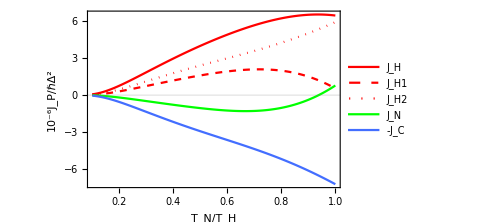
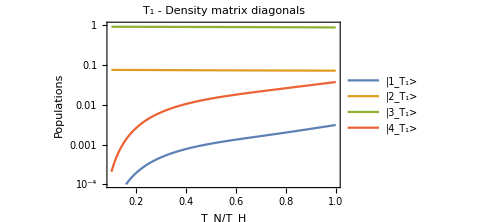
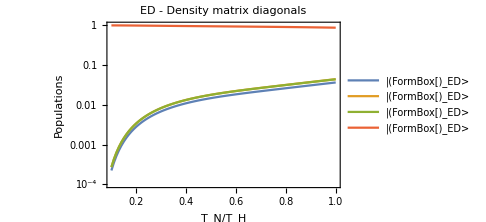
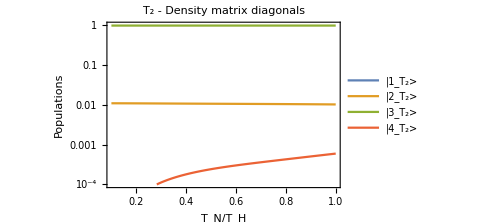
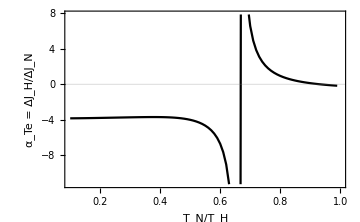

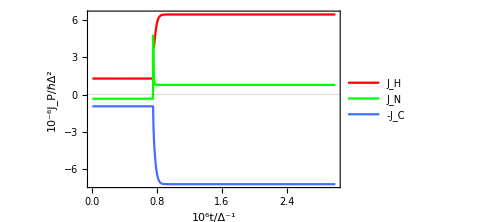
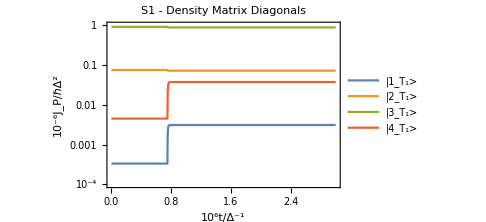
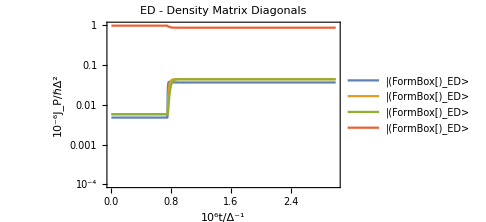

```mathematica
Module[{Thot,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω1,Ω2,γT1s,γT2s,Tcntmin,Tcntmax,Tres},
Thot=0.2Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.001;κcol=0.01;
ωLM1=0.5ωconv;ωMR1=0.6ωconv;ωLM2=0.9ωconv;ωMR2=1.1ωconv;ωEDs=0.2ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv,0.015ωconv};
Ω1=0ωconv;Ω2=0ωconv;
Tcntmin=0.02Tconv;Tcntmax=0.20Tconv;Tres=0.002Tconv;
PlotEngyFlowsWithTcnt[Thot,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω1,Ω2,γT1s,γT2s,Tcntmin,Tcntmax,Tres,True,""]
]
Module[{Thot,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,Ω1,Ω2,ωED,γT1s,γT2s, Tcnt1,Tcnt2,tstart,tchange,tmax},
Thot= 0.2 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.001;κcol=0.01;
ωLM1=0.5ωconv;ωMR1=0.6ωconv;ωLM2=0.9ωconv;ωMR2=1.1ωconv;ωED=0.2ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv,0.015ωconv};
Ω1=0ωconv;Ω2=0ωconv;
Tcnt1=0.05Tconv;Tcnt2=0.2Tconv;
tmax=3.0 10^6/ωconv;tchange=0.25 tmax;tstart=0tmax;
PlotTimeDomainWithT[Thot,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,Ω1,Ω2,ωED,γT1s,γT2s, Tcnt1,Tcnt2,tstart,tchange,tmax]
]
```

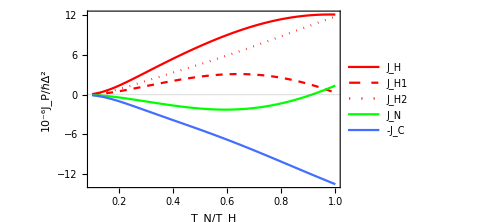
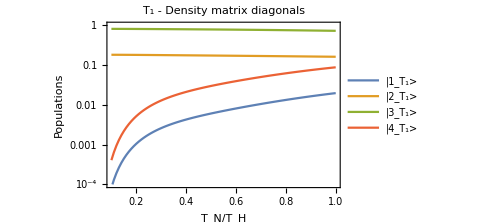
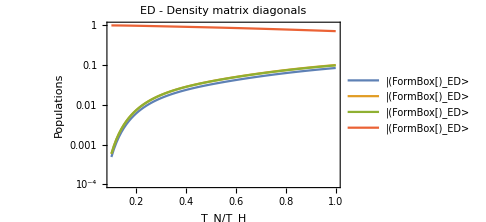
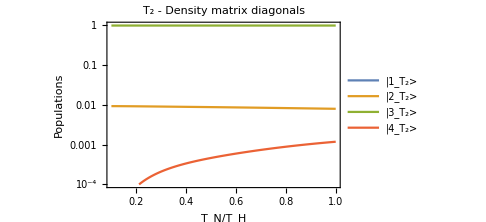
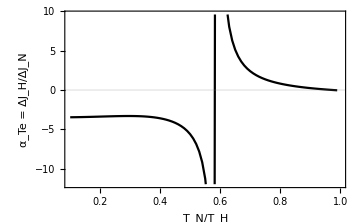

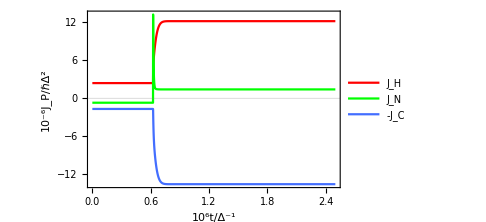
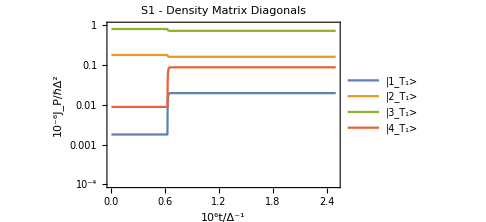
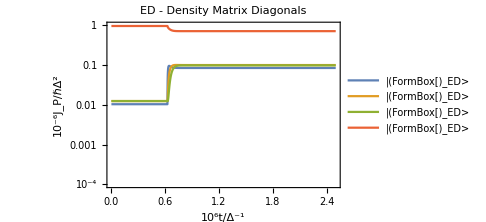

```mathematica
Module[{Thot,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω1,Ω2,γT1s,γT2s,Tcntmin,Tcntmax,Tres},
Thot=0.2Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.001;κcol=0.01;
ωLM1=0.3ωconv;ωMR1=0.4ωconv;ωLM2=(1- 0.4/6)ωconv;ωMR2=(1+ 0.4/6)ωconv;ωEDs=(0.4/3)ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv,0.015ωconv};
Ω1=0ωconv;Ω2=0ωconv;
Tcntmin=0.02Tconv;Tcntmax=0.20Tconv;Tres=0.002Tconv;
PlotEngyFlowsWithTcnt[Thot,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω1,Ω2,γT1s,γT2s,Tcntmin,Tcntmax,Tres,True,""]
]
Module[{Thot,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,Ω1,Ω2,ωED,γT1s,γT2s, Tcnt1,Tcnt2,tstart,tchange,tmax},
Thot=0.2Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.001;κcol=0.01;
ωLM1=0.3ωconv;ωMR1=0.4ωconv;ωLM2=(1- 0.4/6)ωconv;ωMR2=(1+ 0.4/6)ωconv;ωED=(0.4/3)ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv,0.015ωconv};
Ω1=0ωconv;Ω2=0ωconv;
Tcnt1=0.05Tconv;Tcnt2=0.2Tconv;
tmax=2.5 10^6/ωconv;tchange=0.25 tmax;tstart=0tmax;
PlotTimeDomainWithT[Thot,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,Ω1,Ω2,ωED,γT1s,γT2s, Tcnt1,Tcnt2,tstart,tchange,tmax]
]
```

### Energy flow under different field strengths

Energy flows when ω_2 is changed from below ω_3 to above ω_3, keeping the γs constant,

```mathematica
PlotEngyFlowsWithΩ1[Thot_,Tcnt_,Tcol_,κhot_,κcnt_,κcol_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,ωEDs_,Ω2s_,γT1s_,γT2s_,Ω1min_,Ω1max_,Ωres_,legends_,title_]:=Module[{tempx,tempy,combflows,denmatT1,denmatED,denmatT2,amplif},
tempx=Table[Ω1/(κhot ωconv),{Ω1,Ω1min,Ω1max,Ωres},{i,1,9}];
tempy=ParallelTable[varFunc[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω1,Ω2s,γT1s,γT2s,unitassum],{Ω1,Ω1min,Ω1max,Ωres}];
combflows=Table[MapThread[List,{tempx[[;;,i]],10^6 tempy[[;;,2,i]]}],{i,1,6}];
denmatT1=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,6,i]]}],{i,1,4}];
denmatED=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,7,i]]}],{i,1,Ns}];
denmatT2=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,8,i]]}],{i,1,4}];
amplif=MapThread[List,{Drop[tempx[[;;,1]],-1],Differences[tempy[[;;,2,1]]]/Differences[tempy[[;;,2,6]]]}];
{
ListPlot[combflows,
PlotRange->{{Ω1min/(κhot ωconv),Ω1max/(κhot ωconv)},Full},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["Ω_F/κΔ",FontFamily->"Times New Roman",FontSize->16],
		Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style[title,FontFamily->"Times New Roman",FontSize->14.5],
PlotStyle->{{Red},{Red,Dashed},{Red,Dotted},{Green},{BlueC},PurpleC},
PlotLegends->legends &&{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_H^T_1",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_H^T_2",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F",FontFamily->"Times New Roman",FontSize->14.5]}],
ListLogPlot[denmatT1,
PlotRange->{{Ω1min/(κhot ωconv),Ω1max/(κhot ωconv)},{0.0001,1}},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["Ω_F/κΔ",FontFamily->"Times New Roman",FontSize->16],
		Style["Populations",FontFamily->"Times New Roman",FontSize->16]},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style["T_1 - Density matrix diagonals",FontFamily->"Times New Roman",FontSize->14.5],
PlotLegends->legends &&{
Style["|1_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_1>",FontFamily->"Times New Roman",FontSize->14.5]}],
ListLogPlot[denmatED,
PlotRange->{{Ω1min/(κhot ωconv),Ω1max/(κhot ωconv)},{0.0001,1}},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["Ω_F/κΔ",FontFamily->"Times New Roman",FontSize->16],
		Style["Populations",FontFamily->"Times New Roman",FontSize->16]},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style["ED - Density matrix diagonals",FontFamily->"Times New Roman",FontSize->14.5],
PlotLegends->legends &&Table[Style[StringForm["|(``)_ED>",Ns-i],FontFamily->"Times New Roman",FontSize->14.5],{i,1,Ns}]],
ListLogPlot[denmatT2,
PlotRange->{{Ω1min/(κhot ωconv),Ω1max/(κhot ωconv)},{0.0001,1}},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["Ω_F/κΔ",FontFamily->"Times New Roman",FontSize->16],
		Style["Populations",FontFamily->"Times New Roman",FontSize->16]},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style["T_2 - Density matrix diagonals",FontFamily->"Times New Roman",FontSize->14.5],
PlotLegends->legends &&{
Style["|1_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_2>",FontFamily->"Times New Roman",FontSize->14.5]}],
ListPlot[amplif,
	ImageSize->Medium,
	PlotRange->{{Ω1min/(κhot ωconv),Ω1max/(κhot ωconv)},Full},
	Axes->False,
	Frame-> {{True,False},{True,False}},
	FrameLabel->{
		Style["Ω_F/κΔ",FontFamily->"Times New Roman",FontSize->15],
		Style["α_Op = ΔJ_H/ΔJ_F",FontFamily->"Times New Roman",FontSize->15]},
	FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
	GridLines->{None,{0}},
	PlotStyle->{Black},
	Joined->True]
}
]
```

### Time domain behaviors

Plot time domain

```mathematica
PlotTimeDomainWithΩ1[Thots_,Tcnts_,Tcols_,κhots_,κcnts_,κcols_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,Ω2_,ωEDs_,γT1s_,γT2s_, Ωcnt1s_,Ωcnt2s_,tstart_,tchange_,tmax_]:=Module[{timeassum,sysassum,indsysassum,motioneqs,initMatrix,indmotioneqs,initconditions,indinitconditions,dynamics,inddynamics,tempgraph,denmatS1graph,denmatS2graph,denmatEDgraph,flowgraph,inddenmatgraph,indflowgraph},
timeassum:={
Ωcnt-> Piecewise[{{Ωcnt1s,t<tchange},{Ωcnt2s,t>tchange}}]
};
sysassum =Flatten[ {
Subscript[T, 1]-> Thots,Subscript[T, 2]-> Tcnts,Subscript[T, 3]-> Tcols,
Subscript[κ, 1]->κhots,Subscript[κ, 2]->κcnts,Subscript[κ, 3]->κcols,
Subscript[ωLM, 1]->ωLM1,Subscript[ωMR, 1]->ωMR1,
Subscript[ωLM, 2]->ωLM2,Subscript[ωMR, 2]->ωMR2,
Subscript[Ω, 1]->Ωcnt,Subscript[Ω, 2]->Ω2,
ωED->ωEDs,
Table[γT1[i]->γT1s[[i+1]],{i,0,Ns-1-p}],Table[γT2[i]->γT2s[[i+1]],{i,0,Ns-1-q}]
}];

initMatrix=findInitMatrix[Thots,Tcnts,Tcols,κhots,κcnts,κcols,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ωcnt1s,Ω2,γT1s,γT2s,unitassum];

motioneqs=sol//.Flatten[{NBEassum,unitassum,timeassum,sysassum,Jassum}];
initconditions={Table[Subscript[ρ, i,j][0]==initMatrix[[1,i,j]],{i,1,16Ns},{j,1,16Ns}]}/.sysassum;

dynamics = NDSolve[
Flatten[{motioneqs,initconditions}]
,Flatten[Table[Subscript[ρ, i,j],{i,1,16Ns},{j,1,16Ns}]],{t,tstart,tmax}
];

denmatS1graph=Flatten[Table[PartialTraceT1[ρMatrix[10^6 t],4,Ns,4][[i,i]],{i,1,4}]/.dynamics];
denmatEDgraph=Flatten[Table[PartialTraceED[ρMatrix[10^6 t],4,Ns,4][[i,i]],{i,1,Ns}]/.dynamics];
denmatS2graph=Flatten[Table[PartialTraceT2[ρMatrix[10^6 t],4,Ns,4][[i,i]],{i,1,4}]/.dynamics];

flowgraph=Re[Flatten[10^6{
Subscript[EngyFlowIn, 1,1][ρMatrix[t]]+Subscript[EngyFlowIn, 1,2][ρMatrix[t]],
Subscript[EngyFlowIn, 2][ρMatrix[t]],Subscript[EngyFlowIn, 3][ρMatrix[t]],
Subscript[EngyFlowIn, 4,1][ρMatrix[t]]+Subscript[EngyFlowIn, 4,2][ρMatrix[t]]}//.Flatten[{NBEassum,unitassum,timeassum,sysassum,Jassum}]/.dynamics]]/.t->10^6 t;

{
timedom=Plot[flowgraph,{t,0,10^-6 tmax},
ImageSize->Medium,
PlotRange->{Automatic, Automatic},
PlotLegends->{
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F",FontFamily->"Times New Roman",FontSize->14.5]},
Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]}, 
GridLines->{None,{0}},
PlotStyle->{Red,Green,BlueC,PurpleC}],
LogPlot[denmatS1graph,{t,0,10^-6 tmax},
ImageSize->Medium,
	PlotLabel->  Style["S1 - Density Matrix Diagonals",FontFamily->"Times New Roman",FontSize->14.5],
	PlotRange-> {0.0001,1},
	Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]}, 
GridLines->{None,{0}},
PlotLegends->{
Style["|1_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_1>",FontFamily->"Times New Roman",FontSize->14.5]}
],
LogPlot[denmatEDgraph,{t,0,10^-6 tmax},
	ImageSize->Medium,
	PlotLabel->  Style["ED - Density Matrix Diagonals",FontFamily->"Times New Roman",FontSize->14.5],
	PlotRange-> {0.0001,1},
	Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]}, 
GridLines->{None,{0}},
PlotLegends->Table[Style[StringForm["|(``)_ED>",Ns-i],FontFamily->"Times New Roman",FontSize->14.5],{i,1,Ns}]
],
LogPlot[denmatS2graph,{t,0,10^-6 tmax},
	ImageSize->Medium,
	PlotLabel->  Style["S2 - Density Matrix Diagonals",FontFamily->"Times New Roman",FontSize->14.5],
	PlotRange-> {0.0001,1},
	Frame-> {{True,False},{True,False}},
FrameStyle->Directive[Darker[Gray],15,FontFamily->"Times New Roman"],
FrameLabel->{
Style["10^6t/Δ^-1",FontFamily->"Times New Roman",FontSize->16],
Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->16]}, 
GridLines->{None,{0}},
PlotLegends->{
Style["|1_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_2>",FontFamily->"Times New Roman",FontSize->14.5]}
]
}
]
```

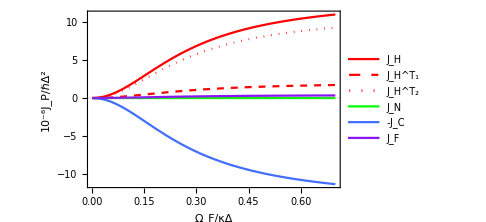
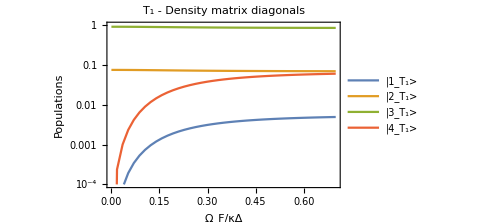
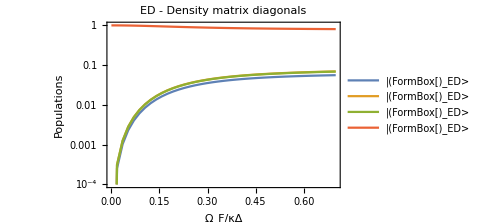
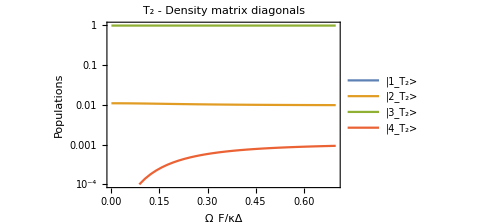
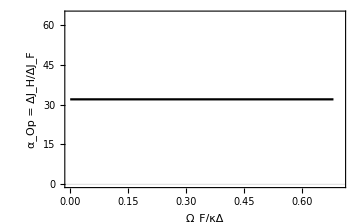

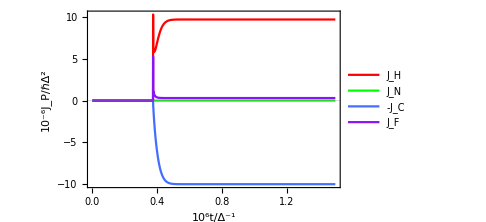
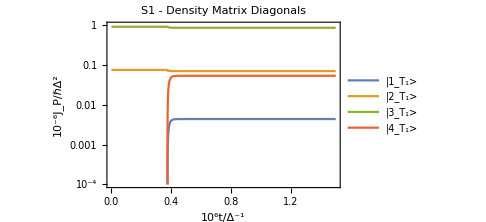
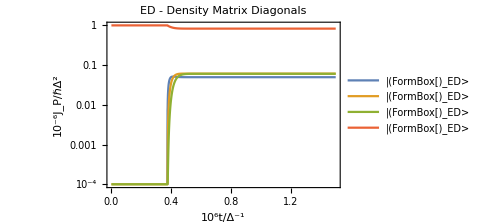

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.00;κcol=0.01;
ωLM1=0.5ωconv;ωMR1=0.6ωconv;ωLM2=0.9ωconv;ωMR2=1.1ωconv;ωEDs=0.20ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv,0.015ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.000175ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,True,""]
]
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol, ωLM1,ωMR1,ωLM2,ωMR2,Ω2,ωED,γT1s,γT2s, Ωcnt1,Ωcnt2,tstart,tchange,tmax},
Thot= 0.2 Tconv;Tcnt= 0.02 Tconv;Tcol= 0.02 Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;
ωLM1=0.5ωconv;ωMR1=0.6ωconv;ωLM2=0.9ωconv;ωMR2=1.1ωconv;ωED=0.20ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv,0.015ωconv};
Ωcnt1=0.01ωconv*κhot;Ωcnt2=0.5ωconv*κhot;
Ω2=0ωconv;
tmax=1.5 10^6/ωconv;tchange=0.25 tmax;tstart=0tmax;
PlotTimeDomainWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,Ω2, ωED,γT1s,γT2s,Ωcnt1,Ωcnt2,tstart,tchange,tmax]
]
```

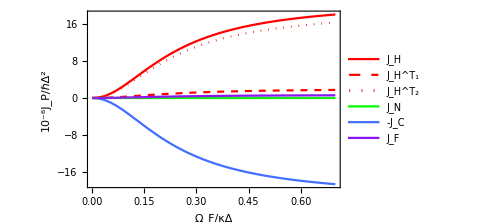
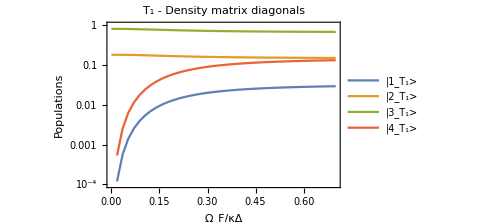
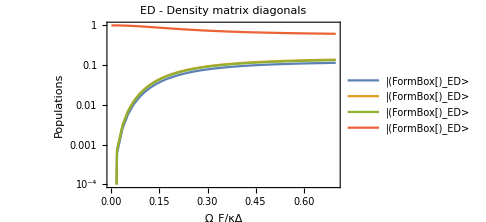
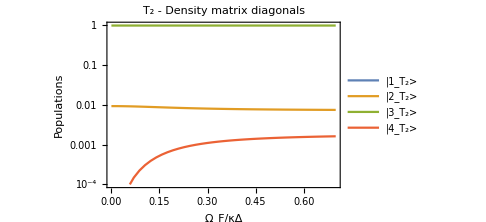
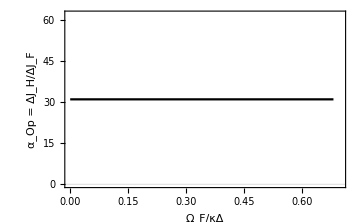

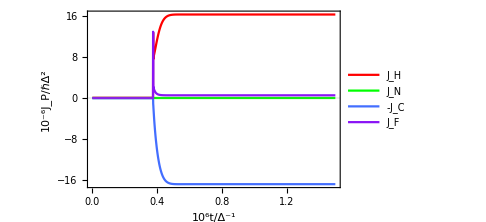
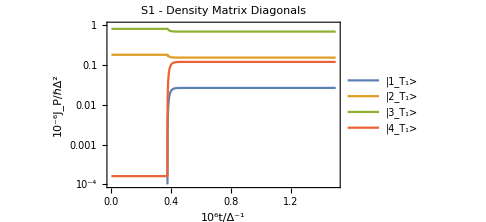
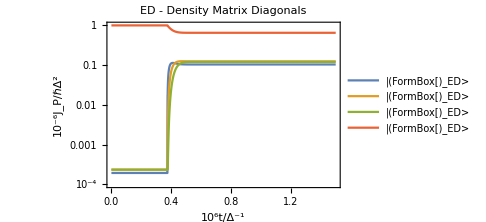

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.00;κcol=0.01;
ωLM1=0.3ωconv;ωMR1=0.4ωconv;ωLM2=(1- 0.4/6)ωconv;ωMR2=(1+ 0.4/6)ωconv;ωEDs=(0.4/3)ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv,0.015ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.000175ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,True,""]
]
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol, ωLM1,ωMR1,ωLM2,ωMR2,Ω2,ωED,γT1s,γT2s, Ωcnt1,Ωcnt2,tstart,tchange,tmax},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.00;κcol=0.01;
ωLM1=0.3ωconv;ωMR1=0.4ωconv;ωLM2=(1- 0.4/6)ωconv;ωMR2=(1+ 0.4/6)ωconv;ωED=(0.4/3)ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv,0.015ωconv};
Ωcnt1=0.01ωconv*κhot;Ωcnt2=0.5ωconv*κhot;
Ω2=0ωconv;
tmax=1.5 10^6/ωconv;tchange=0.25 tmax;tstart=0tmax;
PlotTimeDomainWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,Ω2, ωED,γT1s,γT2s,Ωcnt1,Ωcnt2,tstart,tchange,tmax]
]
```

#### For different energy divider coupling strengths

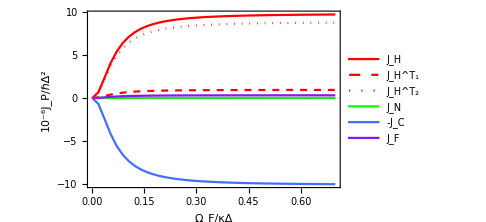
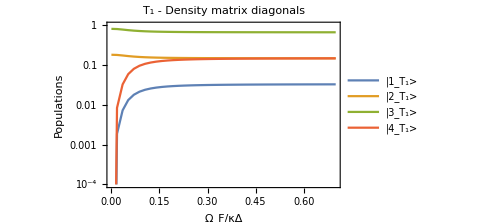
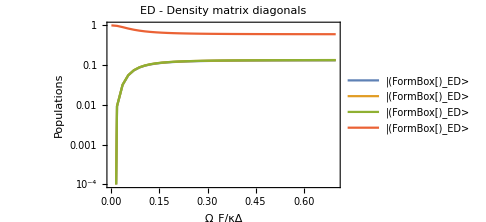
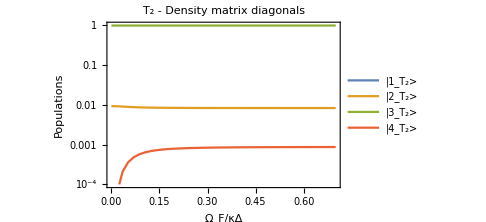
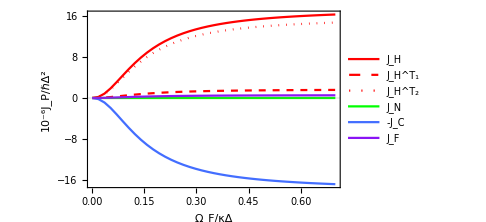
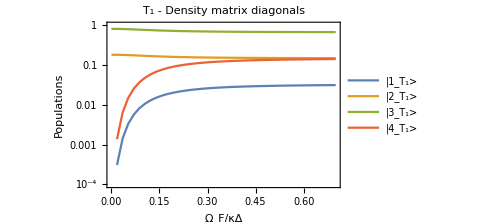
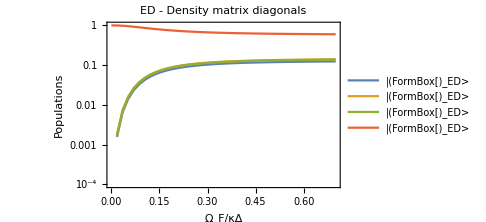
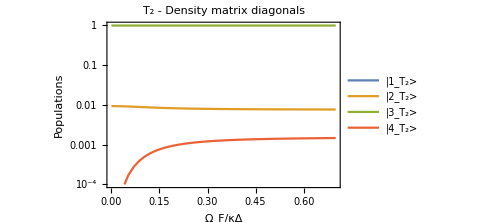
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
{
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.00;κcol=0.01;
ωLM1=0.3ωconv;ωMR1=0.4ωconv;ωLM2=(1- 0.4/6)ωconv;ωMR2=(1+ 0.4/6)ωconv;ωEDs=(0.4/3)ωconv;
γT1s={0.005ωconv};
γT2s={0.005ωconv,0.005ωconv,0.005ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.000175ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,True,""]
],
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.00;κcol=0.01;
ωLM1=0.3ωconv;ωMR1=0.4ωconv;ωLM2=(1- 0.4/6)ωconv;ωMR2=(1+ 0.4/6)ωconv;ωEDs=(0.4/3)ωconv;
γT1s={0.010ωconv};
γT2s={0.010ωconv,0.010ωconv,0.010ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.000175ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,True,""]
],
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.00;κcol=0.01;
ωLM1=0.3ωconv;ωMR1=0.4ωconv;ωLM2=(1- 0.4/6)ωconv;ωMR2=(1+ 0.4/6)ωconv;ωEDs=(0.4/3)ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv,0.015ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.000175ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,True,""]
],
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.00;κcol=0.01;
ωLM1=0.3ωconv;ωMR1=0.4ωconv;ωLM2=(1- 0.4/6)ωconv;ωMR2=(1+ 0.4/6)ωconv;ωEDs=(0.4/3)ωconv;
γT1s={0.025ωconv};
γT2s={0.025ωconv,0.025ωconv,0.025ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.000175ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,True,""]
]
}
```